```mathematica
Quit[];
```

```mathematica
SetOptions[$FrontEnd,EvaluationCompletionAction->"ShowTiming"]
```

# Static spherically symmetric spheres: Parameter space analysis

```mathematica
(* This notebook performs a parameter space analysis for the radial speeds of sound for the matter fluid for each solution in our paper. *)
```

## Solution I: Reconstructing from interior Schwarzschild-Tolman IV solution

## Full function for the radial speed of sound for the matter fluid

```mathematica
c2mrfun[α_,μ1_,ℛ_,c_,A_,r_]:=(-((4 ℛ^4 ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))) (-8 r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) α (-3+r^2 μ1) (2 r μ1+(c r μ1)/(√(3-r^2 μ1))) (-6+3 r^2 μ1-2 c √(3-r^2 μ1))-8 r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) α (-3+r^2 μ1) (6 r μ1+(2 c r μ1)/(√(3-r^2 μ1))) (-3+r^2 μ1-c √(3-r^2 μ1))-16 r^3 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) α μ1 (-6+3 r^2 μ1-2 c √(3-r^2 μ1)) (-3+r^2 μ1-c √(3-r^2 μ1))-8 r^2 (4 A^2 r+8 r^3) α (-3+r^2 μ1) (-6+3 r^2 μ1-2 c √(3-r^2 μ1)) (-3+r^2 μ1-c √(3-r^2 μ1))-16 r (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) α (-3+r^2 μ1) (-6+3 r^2 μ1-2 c √(3-r^2 μ1)) (-3+r^2 μ1-c √(3-r^2 μ1))-16 (A^2+2 r^2)^2 ℛ^2 α (-3+r^2 μ1) (-2 r μ1-(c r μ1)/(√(3-r^2 μ1))) (3-r^2 μ1+c √(3-r^2 μ1))-16 r (A^2+2 r^2)^2 ℛ^2 α μ1 (3-r^2 μ1+c √(3-r^2 μ1))^2-64 r (A^2+2 r^2) ℛ^2 α (-3+r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+2 r^2 (A^2+2 r^2)^2 ℛ^2 (3-r^2 μ1) (-4 r μ1-(2 c r μ1)/(√(3-r^2 μ1))) (6-2 r^2 μ1+2 c √(3-r^2 μ1))-2 r^3 (A^2+2 r^2)^2 ℛ^2 μ1 (6-2 r^2 μ1+2 c √(3-r^2 μ1))^2+8 r^3 (A^2+2 r^2) ℛ^2 (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^2+2 r (A^2+2 r^2)^2 ℛ^2 (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^2+8 (A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) α √(3-r^2 μ1) (-3 c^2 r μ1 √(3-r^2 μ1)+3 √(3-r^2 μ1) (-10 r μ1+4 r^3 μ1^2)+c (-42 r μ1+16 r^3 μ1^2)-(3 r μ1 (3-5 r^2 μ1+r^4 μ1^2))/(√(3-r^2 μ1)))-1/(√(3-r^2 μ1))8 r (A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) α μ1 (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))+16 r (A^2+r^2) (A^2+2 r^2) α √(3-r^2 μ1) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))+32 r (A^2+r^2) (r^2-ℛ^2) α √(3-r^2 μ1) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))+16 r (A^2+2 r^2) (r^2-ℛ^2) α √(3-r^2 μ1) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))+4 ℛ^4 (r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (-6 r μ1-(2 c r μ1)/(√(3-r^2 μ1))) (3-r^2 μ1+c √(3-r^2 μ1))+2 (A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (-2 r μ1-(c r μ1)/(√(3-r^2 μ1))) (3-r^2 μ1+c √(3-r^2 μ1))-(r (A^2+2 r^2)^2 ℛ^2 μ1 (3-r^2 μ1+c √(3-r^2 μ1))^2)/(√(3-r^2 μ1))+8 r (A^2+2 r^2) ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (-2 r μ1-(c r μ1)/(√(3-r^2 μ1))) (6-3 r^2 μ1+2 c √(3-r^2 μ1))-1/(√(3-r^2 μ1))r^3 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) μ1 (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+r^2 (4 A^2 r+8 r^3) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+2 r (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (-3 c^2 r μ1 √(3-r^2 μ1)+3 √(3-r^2 μ1) (-10 r μ1+4 r^3 μ1^2)+c (-42 r μ1+16 r^3 μ1^2)-(3 r μ1 (3-5 r^2 μ1+r^4 μ1^2))/(√(3-r^2 μ1)))+2 r (A^2+r^2) (A^2+2 r^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))+4 r (A^2+r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))+2 r (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))) (-8 r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) α (-3+r^2 μ1) (-6+3 r^2 μ1-2 c √(3-r^2 μ1)) (-3+r^2 μ1-c √(3-r^2 μ1))-8 (A^2+2 r^2)^2 ℛ^2 α (-3+r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^2+2 r^2)^2 ℛ^2 (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^2+8 (A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) α √(3-r^2 μ1) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))-4 r^2 ℛ^2 √(3-r^2 μ1) (A^4 (2 c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (6-6 r^2 μ1+ℛ^2 μ1+r^4 μ1^2)+c (36-30 r^2 μ1+3 ℛ^2 μ1+5 r^4 μ1^2))+2 r^4 (2 c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (6-6 r^2 μ1+ℛ^2 μ1+r^4 μ1^2)+c (36-30 r^2 μ1+3 ℛ^2 μ1+5 r^4 μ1^2))+A^2 (2 c^2 (2 r^2+ℛ^2) (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (6 ℛ^2+2 r^6 μ1^2+r^4 μ1 (-13+ℛ^2 μ1)-2 r^2 (-6+ℛ^2 μ1))+c (36 ℛ^2+10 r^6 μ1^2-18 r^2 (-4+ℛ^2 μ1)+r^4 μ1 (-63+5 ℛ^2 μ1)))) (8 r^2 (A^2+2 r^2)^2 ℛ^4 √(3-r^2 μ1) (-2 r μ1-(c r μ1)/(√(3-r^2 μ1))) (3-r^2 μ1+c √(3-r^2 μ1))-(4 r^3 (A^2+2 r^2)^2 ℛ^4 μ1 (3-r^2 μ1+c √(3-r^2 μ1))^2)/(√(3-r^2 μ1))+32 r^3 (A^2+2 r^2) ℛ^4 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+8 r (A^2+2 r^2)^2 ℛ^4 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+16 ℛ^2 α (r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (-6 r μ1-(2 c r μ1)/(√(3-r^2 μ1))) (3-r^2 μ1+c √(3-r^2 μ1))+2 (A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (-2 r μ1-(c r μ1)/(√(3-r^2 μ1))) (3-r^2 μ1+c √(3-r^2 μ1))-(r (A^2+2 r^2)^2 ℛ^2 μ1 (3-r^2 μ1+c √(3-r^2 μ1))^2)/(√(3-r^2 μ1))+8 r (A^2+2 r^2) ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (-2 r μ1-(c r μ1)/(√(3-r^2 μ1))) (6-3 r^2 μ1+2 c √(3-r^2 μ1))-1/(√(3-r^2 μ1))r^3 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) μ1 (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+r^2 (4 A^2 r+8 r^3) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+2 r (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (-3 c^2 r μ1 √(3-r^2 μ1)+3 √(3-r^2 μ1) (-10 r μ1+4 r^3 μ1^2)+c (-42 r μ1+16 r^3 μ1^2)-(3 r μ1 (3-5 r^2 μ1+r^4 μ1^2))/(√(3-r^2 μ1)))+2 r (A^2+r^2) (A^2+2 r^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))+4 r (A^2+r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))+2 r (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))))-4 r^2 ℛ^2 √(3-r^2 μ1) (A^4 (-6 c^2 r μ1 √(3-r^2 μ1)+3 √(3-r^2 μ1) (-12 r μ1+4 r^3 μ1^2)+c (-60 r μ1+20 r^3 μ1^2)-(3 r μ1 (6-6 r^2 μ1+ℛ^2 μ1+r^4 μ1^2))/(√(3-r^2 μ1)))+2 r^4 (-6 c^2 r μ1 √(3-r^2 μ1)+3 √(3-r^2 μ1) (-12 r μ1+4 r^3 μ1^2)+c (-60 r μ1+20 r^3 μ1^2)-(3 r μ1 (6-6 r^2 μ1+ℛ^2 μ1+r^4 μ1^2))/(√(3-r^2 μ1)))+8 r^3 (2 c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (6-6 r^2 μ1+ℛ^2 μ1+r^4 μ1^2)+c (36-30 r^2 μ1+3 ℛ^2 μ1+5 r^4 μ1^2))+A^2 (-6 c^2 r (2 r^2+ℛ^2) μ1 √(3-r^2 μ1)+8 c^2 r (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (12 r^5 μ1^2+4 r^3 μ1 (-13+ℛ^2 μ1)-4 r (-6+ℛ^2 μ1))-(3 r μ1 (6 ℛ^2+2 r^6 μ1^2+r^4 μ1 (-13+ℛ^2 μ1)-2 r^2 (-6+ℛ^2 μ1)))/(√(3-r^2 μ1))+c (60 r^5 μ1^2-36 r (-4+ℛ^2 μ1)+4 r^3 μ1 (-63+5 ℛ^2 μ1)))) (4 r^2 (A^2+2 r^2)^2 ℛ^4 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+16 ℛ^2 α ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))))+1/(√(3-r^2 μ1))4 r^3 ℛ^2 μ1 (A^4 (2 c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (6-6 r^2 μ1+ℛ^2 μ1+r^4 μ1^2)+c (36-30 r^2 μ1+3 ℛ^2 μ1+5 r^4 μ1^2))+2 r^4 (2 c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (6-6 r^2 μ1+ℛ^2 μ1+r^4 μ1^2)+c (36-30 r^2 μ1+3 ℛ^2 μ1+5 r^4 μ1^2))+A^2 (2 c^2 (2 r^2+ℛ^2) (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (6 ℛ^2+2 r^6 μ1^2+r^4 μ1 (-13+ℛ^2 μ1)-2 r^2 (-6+ℛ^2 μ1))+c (36 ℛ^2+10 r^6 μ1^2-18 r^2 (-4+ℛ^2 μ1)+r^4 μ1 (-63+5 ℛ^2 μ1)))) (4 r^2 (A^2+2 r^2)^2 ℛ^4 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+16 ℛ^2 α ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))))-8 r ℛ^2 √(3-r^2 μ1) (A^4 (2 c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (6-6 r^2 μ1+ℛ^2 μ1+r^4 μ1^2)+c (36-30 r^2 μ1+3 ℛ^2 μ1+5 r^4 μ1^2))+2 r^4 (2 c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (6-6 r^2 μ1+ℛ^2 μ1+r^4 μ1^2)+c (36-30 r^2 μ1+3 ℛ^2 μ1+5 r^4 μ1^2))+A^2 (2 c^2 (2 r^2+ℛ^2) (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (6 ℛ^2+2 r^6 μ1^2+r^4 μ1 (-13+ℛ^2 μ1)-2 r^2 (-6+ℛ^2 μ1))+c (36 ℛ^2+10 r^6 μ1^2-18 r^2 (-4+ℛ^2 μ1)+r^4 μ1 (-63+5 ℛ^2 μ1)))) (4 r^2 (A^2+2 r^2)^2 ℛ^4 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+16 ℛ^2 α ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))))+32 ℛ^4 α (6-3 r^2 μ1+2 c √(3-r^2 μ1)) (4 r^2 (A^2+r^2) (A^2+2 r^2) (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1)) (r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (-6 r μ1-(2 c r μ1)/(√(3-r^2 μ1))) (3-r^2 μ1+c √(3-r^2 μ1))+2 (A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (-2 r μ1-(c r μ1)/(√(3-r^2 μ1))) (3-r^2 μ1+c √(3-r^2 μ1))-(r (A^2+2 r^2)^2 ℛ^2 μ1 (3-r^2 μ1+c √(3-r^2 μ1))^2)/(√(3-r^2 μ1))+8 r (A^2+2 r^2) ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (-2 r μ1-(c r μ1)/(√(3-r^2 μ1))) (6-3 r^2 μ1+2 c √(3-r^2 μ1))-1/(√(3-r^2 μ1))r^3 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) μ1 (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+r^2 (4 A^2 r+8 r^3) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+2 r (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (-3 c^2 r μ1 √(3-r^2 μ1)+3 √(3-r^2 μ1) (-10 r μ1+4 r^3 μ1^2)+c (-42 r μ1+16 r^3 μ1^2)-(3 r μ1 (3-5 r^2 μ1+r^4 μ1^2))/(√(3-r^2 μ1)))+2 r (A^2+r^2) (A^2+2 r^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))+4 r (A^2+r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))+2 r (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))-8 r^2 (A^2+r^2) (r^2-ℛ^2) (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1)) (r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (-6 r μ1-(2 c r μ1)/(√(3-r^2 μ1))) (3-r^2 μ1+c √(3-r^2 μ1))+2 (A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (-2 r μ1-(c r μ1)/(√(3-r^2 μ1))) (3-r^2 μ1+c √(3-r^2 μ1))-(r (A^2+2 r^2)^2 ℛ^2 μ1 (3-r^2 μ1+c √(3-r^2 μ1))^2)/(√(3-r^2 μ1))+8 r (A^2+2 r^2) ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (-2 r μ1-(c r μ1)/(√(3-r^2 μ1))) (6-3 r^2 μ1+2 c √(3-r^2 μ1))-1/(√(3-r^2 μ1))r^3 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) μ1 (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+r^2 (4 A^2 r+8 r^3) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+2 r (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (-3 c^2 r μ1 √(3-r^2 μ1)+3 √(3-r^2 μ1) (-10 r μ1+4 r^3 μ1^2)+c (-42 r μ1+16 r^3 μ1^2)-(3 r μ1 (3-5 r^2 μ1+r^4 μ1^2))/(√(3-r^2 μ1)))+2 r (A^2+r^2) (A^2+2 r^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))+4 r (A^2+r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))+2 r (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))+4 r^2 (A^2+2 r^2) (r^2-ℛ^2) (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1)) (r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (-6 r μ1-(2 c r μ1)/(√(3-r^2 μ1))) (3-r^2 μ1+c √(3-r^2 μ1))+2 (A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (-2 r μ1-(c r μ1)/(√(3-r^2 μ1))) (3-r^2 μ1+c √(3-r^2 μ1))-(r (A^2+2 r^2)^2 ℛ^2 μ1 (3-r^2 μ1+c √(3-r^2 μ1))^2)/(√(3-r^2 μ1))+8 r (A^2+2 r^2) ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (-2 r μ1-(c r μ1)/(√(3-r^2 μ1))) (6-3 r^2 μ1+2 c √(3-r^2 μ1))-1/(√(3-r^2 μ1))r^3 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) μ1 (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+r^2 (4 A^2 r+8 r^3) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+2 r (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (-3 c^2 r μ1 √(3-r^2 μ1)+3 √(3-r^2 μ1) (-10 r μ1+4 r^3 μ1^2)+c (-42 r μ1+16 r^3 μ1^2)-(3 r μ1 (3-5 r^2 μ1+r^4 μ1^2))/(√(3-r^2 μ1)))+2 r (A^2+r^2) (A^2+2 r^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))+4 r (A^2+r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))+2 r (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))-2 (A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1)) (r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (-6 r μ1-(2 c r μ1)/(√(3-r^2 μ1))) (3-r^2 μ1+c √(3-r^2 μ1))+2 (A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (-2 r μ1-(c r μ1)/(√(3-r^2 μ1))) (3-r^2 μ1+c √(3-r^2 μ1))-(r (A^2+2 r^2)^2 ℛ^2 μ1 (3-r^2 μ1+c √(3-r^2 μ1))^2)/(√(3-r^2 μ1))+8 r (A^2+2 r^2) ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (-2 r μ1-(c r μ1)/(√(3-r^2 μ1))) (6-3 r^2 μ1+2 c √(3-r^2 μ1))-1/(√(3-r^2 μ1))r^3 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) μ1 (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+r^2 (4 A^2 r+8 r^3) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+2 r (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (-3 c^2 r μ1 √(3-r^2 μ1)+3 √(3-r^2 μ1) (-10 r μ1+4 r^3 μ1^2)+c (-42 r μ1+16 r^3 μ1^2)-(3 r μ1 (3-5 r^2 μ1+r^4 μ1^2))/(√(3-r^2 μ1)))+2 r (A^2+r^2) (A^2+2 r^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))+4 r (A^2+r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))+2 r (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))+4 r^2 (A^2+r^2) (A^2+2 r^2) (3-r^2 μ1) (-4 r μ1-(2 c r μ1)/(√(3-r^2 μ1))) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))-8 r^2 (A^2+r^2) (r^2-ℛ^2) (3-r^2 μ1) (-4 r μ1-(2 c r μ1)/(√(3-r^2 μ1))) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))+4 r^2 (A^2+2 r^2) (r^2-ℛ^2) (3-r^2 μ1) (-4 r μ1-(2 c r μ1)/(√(3-r^2 μ1))) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))-2 (A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (3-r^2 μ1) (-4 r μ1-(2 c r μ1)/(√(3-r^2 μ1))) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))-8 r^3 (A^2+r^2) (A^2+2 r^2) μ1 (6-2 r^2 μ1+2 c √(3-r^2 μ1)) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))+16 r^3 (A^2+r^2) (r^2-ℛ^2) μ1 (6-2 r^2 μ1+2 c √(3-r^2 μ1)) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))-8 r^3 (A^2+2 r^2) (r^2-ℛ^2) μ1 (6-2 r^2 μ1+2 c √(3-r^2 μ1)) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))+4 r (A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) μ1 (6-2 r^2 μ1+2 c √(3-r^2 μ1)) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))+16 r^3 (A^2+2 r^2) (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1)) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))+4 r (A^2+r^2) (A^2+2 r^2) (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1)) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))-24 r (A^2+r^2) (r^2-ℛ^2) (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1)) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))+4 r (A^2+2 r^2) (r^2-ℛ^2) (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1)) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))-(A^2+2 r^2) (-2 r^4 (A^2+r^2) (r^2-ℛ^2) (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) μ1 (-3+r^2 μ1) (2 c r μ1+(6 r μ1)/(√(3-r^2 μ1))) (-3+r^2 μ1-c √(3-r^2 μ1))+4 r^2 (A^6 (r^2+ℛ^2)+2 r^6 (r^2+ℛ^2)+A^4 (3 r^4+4 r^2 ℛ^2+ℛ^4)+A^2 (2 r^6+9 r^4 ℛ^2-r^2 ℛ^4)) (3-r^2 μ1)^(3/2) (-6 r μ1-(2 c r μ1)/(√(3-r^2 μ1))) (3-r^2 μ1+c √(3-r^2 μ1))^2+8 r^2 (A^6 (r^2+ℛ^2)+2 r^6 (r^2+ℛ^2)+A^4 (3 r^4+4 r^2 ℛ^2+ℛ^4)+A^2 (2 r^6+9 r^4 ℛ^2-r^2 ℛ^4)) (3-r^2 μ1)^(3/2) (-2 r μ1-(c r μ1)/(√(3-r^2 μ1))) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))-12 r^3 (A^6 (r^2+ℛ^2)+2 r^6 (r^2+ℛ^2)+A^4 (3 r^4+4 r^2 ℛ^2+ℛ^4)+A^2 (2 r^6+9 r^4 ℛ^2-r^2 ℛ^4)) μ1 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2 (6-3 r^2 μ1+2 c √(3-r^2 μ1))+4 r^2 (2 A^6 r+4 r^7+12 r^5 (r^2+ℛ^2)+A^4 (12 r^3+8 r ℛ^2)+A^2 (12 r^5+36 r^3 ℛ^2-2 r ℛ^4)) (3-r^2 μ1)^(3/2) (3-r^2 μ1+c √(3-r^2 μ1))^2 (6-3 r^2 μ1+2 c √(3-r^2 μ1))+8 r (A^6 (r^2+ℛ^2)+2 r^6 (r^2+ℛ^2)+A^4 (3 r^4+4 r^2 ℛ^2+ℛ^4)+A^2 (2 r^6+9 r^4 ℛ^2-r^2 ℛ^4)) (3-r^2 μ1)^(3/2) (3-r^2 μ1+c √(3-r^2 μ1))^2 (6-3 r^2 μ1+2 c √(3-r^2 μ1))+3 r^2 (A^2+r^2) (A^2+2 r^2)^2 ℛ^2 (3-r^2 μ1)^(3/2) (-4 r μ1-(2 c r μ1)/(√(3-r^2 μ1))) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^2-6 r^2 (A^2+r^2) (A^2+2 r^2) ℛ^2 (r^2-ℛ^2) (3-r^2 μ1)^(3/2) (-4 r μ1-(2 c r μ1)/(√(3-r^2 μ1))) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^2+3 r^2 (A^2+2 r^2)^2 ℛ^2 (r^2-ℛ^2) (3-r^2 μ1)^(3/2) (-4 r μ1-(2 c r μ1)/(√(3-r^2 μ1))) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^2-3 r^3 (A^2+r^2) (A^2+2 r^2)^2 ℛ^2 μ1 √(3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^3+6 r^3 (A^2+r^2) (A^2+2 r^2) ℛ^2 (r^2-ℛ^2) μ1 √(3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^3-3 r^3 (A^2+2 r^2)^2 ℛ^2 (r^2-ℛ^2) μ1 √(3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^3+4 r^3 (A^2+r^2) (A^2+2 r^2) ℛ^2 (3-r^2 μ1)^(3/2) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^3+4 r^3 (A^2+2 r^2)^2 ℛ^2 (3-r^2 μ1)^(3/2) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^3+2 r (A^2+r^2) (A^2+2 r^2)^2 ℛ^2 (3-r^2 μ1)^(3/2) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^3-8 r^3 (A^2+r^2) ℛ^2 (r^2-ℛ^2) (3-r^2 μ1)^(3/2) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^3+4 r^3 (A^2+2 r^2) ℛ^2 (r^2-ℛ^2) (3-r^2 μ1)^(3/2) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^3-4 r (A^2+r^2) (A^2+2 r^2) ℛ^2 (r^2-ℛ^2) (3-r^2 μ1)^(3/2) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^3+2 r (A^2+2 r^2)^2 ℛ^2 (r^2-ℛ^2) (3-r^2 μ1)^(3/2) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^3-2 r^4 (A^2+r^2) (r^2-ℛ^2) (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) μ1 (-3+r^2 μ1) (2 r μ1+(c r μ1)/(√(3-r^2 μ1))) (-6 √(3-r^2 μ1)+c (-6+r^2 μ1))-4 r^5 (A^2+r^2) (r^2-ℛ^2) (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) μ1^2 (-3+r^2 μ1-c √(3-r^2 μ1)) (-6 √(3-r^2 μ1)+c (-6+r^2 μ1))-2 r^4 (A^2+r^2) (4 A^2 r+8 r^3) (r^2-ℛ^2) μ1 (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (-6 √(3-r^2 μ1)+c (-6+r^2 μ1))-4 r^5 (A^2+r^2) (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) μ1 (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (-6 √(3-r^2 μ1)+c (-6+r^2 μ1))-4 r^5 (r^2-ℛ^2) (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) μ1 (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (-6 √(3-r^2 μ1)+c (-6+r^2 μ1))-8 r^3 (A^2+r^2) (r^2-ℛ^2) (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) μ1 (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (-6 √(3-r^2 μ1)+c (-6+r^2 μ1))+4 r^2 (A^2+r^2)^2 (A^2+2 r^2) (r^2-ℛ^2) (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (-3 c^2 r μ1 √(3-r^2 μ1)+3 √(3-r^2 μ1) (-10 r μ1+4 r^3 μ1^2)+c (-42 r μ1+16 r^3 μ1^2)-(3 r μ1 (3-5 r^2 μ1+r^4 μ1^2))/(√(3-r^2 μ1)))-8 r^2 (A^2+r^2)^2 (r^2-ℛ^2)^2 (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (-3 c^2 r μ1 √(3-r^2 μ1)+3 √(3-r^2 μ1) (-10 r μ1+4 r^3 μ1^2)+c (-42 r μ1+16 r^3 μ1^2)-(3 r μ1 (3-5 r^2 μ1+r^4 μ1^2))/(√(3-r^2 μ1)))+4 (A^2+r^2) (A^2+2 r^2) (r^3-r ℛ^2)^2 (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (-3 c^2 r μ1 √(3-r^2 μ1)+3 √(3-r^2 μ1) (-10 r μ1+4 r^3 μ1^2)+c (-42 r μ1+16 r^3 μ1^2)-(3 r μ1 (3-5 r^2 μ1+r^4 μ1^2))/(√(3-r^2 μ1)))+4 r^2 (A^2+r^2)^2 (A^2+2 r^2) (r^2-ℛ^2) (-3+r^2 μ1) (2 r μ1+(c r μ1)/(√(3-r^2 μ1))) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))-8 r^2 (A^2+r^2)^2 (r^2-ℛ^2)^2 (-3+r^2 μ1) (2 r μ1+(c r μ1)/(√(3-r^2 μ1))) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))+4 (A^2+r^2) (A^2+2 r^2) (r^3-r ℛ^2)^2 (-3+r^2 μ1) (2 r μ1+(c r μ1)/(√(3-r^2 μ1))) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))+8 r^3 (A^2+r^2)^2 (A^2+2 r^2) (r^2-ℛ^2) μ1 (-3+r^2 μ1-c √(3-r^2 μ1)) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))-16 r^3 (A^2+r^2)^2 (r^2-ℛ^2)^2 μ1 (-3+r^2 μ1-c √(3-r^2 μ1)) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))+8 r (A^2+r^2) (A^2+2 r^2) (r^3-r ℛ^2)^2 μ1 (-3+r^2 μ1-c √(3-r^2 μ1)) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))+8 r^3 (A^2+r^2)^2 (A^2+2 r^2) (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))-16 r^3 (A^2+r^2)^2 (r^2-ℛ^2) (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))+16 r^3 (A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))+8 r (A^2+r^2)^2 (A^2+2 r^2) (r^2-ℛ^2) (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))-32 r^3 (A^2+r^2) (r^2-ℛ^2)^2 (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))-16 r (A^2+r^2)^2 (r^2-ℛ^2)^2 (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))+8 (A^2+r^2) (A^2+2 r^2) (3 r^2-ℛ^2) (r^3-r ℛ^2) (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))+16 r (A^2+r^2) (r^3-r ℛ^2)^2 (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))+8 r (A^2+2 r^2) (r^3-r ℛ^2)^2 (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))-2 r^2 (A^2+r^2)^2 (A^2+2 r^2) (r^2-ℛ^2)^2 μ1 (c^2 √(3-r^2 μ1) (30 r μ1-8 r^3 μ1^2)-6 √(3-r^2 μ1) (-24 r μ1+4 r^3 μ1^2)-(c^2 r μ1 (-54+15 r^2 μ1-2 r^4 μ1^2))/(√(3-r^2 μ1))+(6 r μ1 (27-12 r^2 μ1+r^4 μ1^2))/(√(3-r^2 μ1))+c (342 r μ1-108 r^3 μ1^2+12 r^5 μ1^3))-8 r^3 (A^2+r^2)^2 (A^2+2 r^2) (r^2-ℛ^2) μ1 (c^2 √(3-r^2 μ1) (-54+15 r^2 μ1-2 r^4 μ1^2)-6 √(3-r^2 μ1) (27-12 r^2 μ1+r^4 μ1^2)+c (-324+171 r^2 μ1-27 r^4 μ1^2+2 r^6 μ1^3))-8 r^3 (A^2+r^2)^2 (r^2-ℛ^2)^2 μ1 (c^2 √(3-r^2 μ1) (-54+15 r^2 μ1-2 r^4 μ1^2)-6 √(3-r^2 μ1) (27-12 r^2 μ1+r^4 μ1^2)+c (-324+171 r^2 μ1-27 r^4 μ1^2+2 r^6 μ1^3))-8 r^3 (A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2)^2 μ1 (c^2 √(3-r^2 μ1) (-54+15 r^2 μ1-2 r^4 μ1^2)-6 √(3-r^2 μ1) (27-12 r^2 μ1+r^4 μ1^2)+c (-324+171 r^2 μ1-27 r^4 μ1^2+2 r^6 μ1^3))-4 r (A^2+r^2)^2 (A^2+2 r^2) (r^2-ℛ^2)^2 μ1 (c^2 √(3-r^2 μ1) (-54+15 r^2 μ1-2 r^4 μ1^2)-6 √(3-r^2 μ1) (27-12 r^2 μ1+r^4 μ1^2)+c (-324+171 r^2 μ1-27 r^4 μ1^2+2 r^6 μ1^3)))-4 r (4 r^2 (A^6 (r^2+ℛ^2)+2 r^6 (r^2+ℛ^2)+A^4 (3 r^4+4 r^2 ℛ^2+ℛ^4)+A^2 (2 r^6+9 r^4 ℛ^2-r^2 ℛ^4)) (3-r^2 μ1)^(3/2) (3-r^2 μ1+c √(3-r^2 μ1))^2 (6-3 r^2 μ1+2 c √(3-r^2 μ1))+r^2 (A^2+r^2) (A^2+2 r^2)^2 ℛ^2 (3-r^2 μ1)^(3/2) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^3-2 r^2 (A^2+r^2) (A^2+2 r^2) ℛ^2 (r^2-ℛ^2) (3-r^2 μ1)^(3/2) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^3+r^2 (A^2+2 r^2)^2 ℛ^2 (r^2-ℛ^2) (3-r^2 μ1)^(3/2) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^3-2 r^4 (A^2+r^2) (r^2-ℛ^2) (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) μ1 (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (-6 √(3-r^2 μ1)+c (-6+r^2 μ1))+4 r^2 (A^2+r^2)^2 (A^2+2 r^2) (r^2-ℛ^2) (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))-8 r^2 (A^2+r^2)^2 (r^2-ℛ^2)^2 (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))+4 (A^2+r^2) (A^2+2 r^2) (r^3-r ℛ^2)^2 (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))-2 r^2 (A^2+r^2)^2 (A^2+2 r^2) (r^2-ℛ^2)^2 μ1 (c^2 √(3-r^2 μ1) (-54+15 r^2 μ1-2 r^4 μ1^2)-6 √(3-r^2 μ1) (27-12 r^2 μ1+r^4 μ1^2)+c (-324+171 r^2 μ1-27 r^4 μ1^2+2 r^6 μ1^3))))+32 ℛ^4 α (-6 r μ1-(2 c r μ1)/(√(3-r^2 μ1))) (4 r^2 (A^2+r^2) (A^2+2 r^2) (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1)) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))-8 r^2 (A^2+r^2) (r^2-ℛ^2) (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1)) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))+4 r^2 (A^2+2 r^2) (r^2-ℛ^2) (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1)) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))-2 (A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1)) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))-(A^2+2 r^2) (4 r^2 (A^6 (r^2+ℛ^2)+2 r^6 (r^2+ℛ^2)+A^4 (3 r^4+4 r^2 ℛ^2+ℛ^4)+A^2 (2 r^6+9 r^4 ℛ^2-r^2 ℛ^4)) (3-r^2 μ1)^(3/2) (3-r^2 μ1+c √(3-r^2 μ1))^2 (6-3 r^2 μ1+2 c √(3-r^2 μ1))+r^2 (A^2+r^2) (A^2+2 r^2)^2 ℛ^2 (3-r^2 μ1)^(3/2) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^3-2 r^2 (A^2+r^2) (A^2+2 r^2) ℛ^2 (r^2-ℛ^2) (3-r^2 μ1)^(3/2) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^3+r^2 (A^2+2 r^2)^2 ℛ^2 (r^2-ℛ^2) (3-r^2 μ1)^(3/2) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^3-2 r^4 (A^2+r^2) (r^2-ℛ^2) (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) μ1 (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (-6 √(3-r^2 μ1)+c (-6+r^2 μ1))+4 r^2 (A^2+r^2)^2 (A^2+2 r^2) (r^2-ℛ^2) (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))-8 r^2 (A^2+r^2)^2 (r^2-ℛ^2)^2 (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))+4 (A^2+r^2) (A^2+2 r^2) (r^3-r ℛ^2)^2 (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))-2 r^2 (A^2+r^2)^2 (A^2+2 r^2) (r^2-ℛ^2)^2 μ1 (c^2 √(3-r^2 μ1) (-54+15 r^2 μ1-2 r^4 μ1^2)-6 √(3-r^2 μ1) (27-12 r^2 μ1+r^4 μ1^2)+c (-324+171 r^2 μ1-27 r^4 μ1^2+2 r^6 μ1^3)))))/(r^4 (A^2+2 r^2)^4 ℛ^8 (3-r^2 μ1)^(3/2) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^4))+(4 (-4 r μ1-(2 c r μ1)/(√(3-r^2 μ1))) (4 ℛ^4 ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))) (-8 r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) α (-3+r^2 μ1) (-6+3 r^2 μ1-2 c √(3-r^2 μ1)) (-3+r^2 μ1-c √(3-r^2 μ1))-8 (A^2+2 r^2)^2 ℛ^2 α (-3+r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^2+2 r^2)^2 ℛ^2 (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^2+8 (A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) α √(3-r^2 μ1) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))-4 r^2 ℛ^2 √(3-r^2 μ1) (A^4 (2 c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (6-6 r^2 μ1+ℛ^2 μ1+r^4 μ1^2)+c (36-30 r^2 μ1+3 ℛ^2 μ1+5 r^4 μ1^2))+2 r^4 (2 c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (6-6 r^2 μ1+ℛ^2 μ1+r^4 μ1^2)+c (36-30 r^2 μ1+3 ℛ^2 μ1+5 r^4 μ1^2))+A^2 (2 c^2 (2 r^2+ℛ^2) (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (6 ℛ^2+2 r^6 μ1^2+r^4 μ1 (-13+ℛ^2 μ1)-2 r^2 (-6+ℛ^2 μ1))+c (36 ℛ^2+10 r^6 μ1^2-18 r^2 (-4+ℛ^2 μ1)+r^4 μ1 (-63+5 ℛ^2 μ1)))) (4 r^2 (A^2+2 r^2)^2 ℛ^4 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+16 ℛ^2 α ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))))+32 ℛ^4 α (6-3 r^2 μ1+2 c √(3-r^2 μ1)) (4 r^2 (A^2+r^2) (A^2+2 r^2) (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1)) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))-8 r^2 (A^2+r^2) (r^2-ℛ^2) (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1)) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))+4 r^2 (A^2+2 r^2) (r^2-ℛ^2) (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1)) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))-2 (A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1)) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))-(A^2+2 r^2) (4 r^2 (A^6 (r^2+ℛ^2)+2 r^6 (r^2+ℛ^2)+A^4 (3 r^4+4 r^2 ℛ^2+ℛ^4)+A^2 (2 r^6+9 r^4 ℛ^2-r^2 ℛ^4)) (3-r^2 μ1)^(3/2) (3-r^2 μ1+c √(3-r^2 μ1))^2 (6-3 r^2 μ1+2 c √(3-r^2 μ1))+r^2 (A^2+r^2) (A^2+2 r^2)^2 ℛ^2 (3-r^2 μ1)^(3/2) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^3-2 r^2 (A^2+r^2) (A^2+2 r^2) ℛ^2 (r^2-ℛ^2) (3-r^2 μ1)^(3/2) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^3+r^2 (A^2+2 r^2)^2 ℛ^2 (r^2-ℛ^2) (3-r^2 μ1)^(3/2) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^3-2 r^4 (A^2+r^2) (r^2-ℛ^2) (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) μ1 (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (-6 √(3-r^2 μ1)+c (-6+r^2 μ1))+4 r^2 (A^2+r^2)^2 (A^2+2 r^2) (r^2-ℛ^2) (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))-8 r^2 (A^2+r^2)^2 (r^2-ℛ^2)^2 (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))+4 (A^2+r^2) (A^2+2 r^2) (r^3-r ℛ^2)^2 (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))-2 r^2 (A^2+r^2)^2 (A^2+2 r^2) (r^2-ℛ^2)^2 μ1 (c^2 √(3-r^2 μ1) (-54+15 r^2 μ1-2 r^4 μ1^2)-6 √(3-r^2 μ1) (27-12 r^2 μ1+r^4 μ1^2)+c (-324+171 r^2 μ1-27 r^4 μ1^2+2 r^6 μ1^3))))))/(r^4 (A^2+2 r^2)^4 ℛ^8 (3-r^2 μ1)^(3/2) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^5)-(3 μ1 (4 ℛ^4 ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))) (-8 r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) α (-3+r^2 μ1) (-6+3 r^2 μ1-2 c √(3-r^2 μ1)) (-3+r^2 μ1-c √(3-r^2 μ1))-8 (A^2+2 r^2)^2 ℛ^2 α (-3+r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^2+2 r^2)^2 ℛ^2 (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^2+8 (A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) α √(3-r^2 μ1) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))-4 r^2 ℛ^2 √(3-r^2 μ1) (A^4 (2 c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (6-6 r^2 μ1+ℛ^2 μ1+r^4 μ1^2)+c (36-30 r^2 μ1+3 ℛ^2 μ1+5 r^4 μ1^2))+2 r^4 (2 c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (6-6 r^2 μ1+ℛ^2 μ1+r^4 μ1^2)+c (36-30 r^2 μ1+3 ℛ^2 μ1+5 r^4 μ1^2))+A^2 (2 c^2 (2 r^2+ℛ^2) (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (6 ℛ^2+2 r^6 μ1^2+r^4 μ1 (-13+ℛ^2 μ1)-2 r^2 (-6+ℛ^2 μ1))+c (36 ℛ^2+10 r^6 μ1^2-18 r^2 (-4+ℛ^2 μ1)+r^4 μ1 (-63+5 ℛ^2 μ1)))) (4 r^2 (A^2+2 r^2)^2 ℛ^4 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+16 ℛ^2 α ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))))+32 ℛ^4 α (6-3 r^2 μ1+2 c √(3-r^2 μ1)) (4 r^2 (A^2+r^2) (A^2+2 r^2) (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1)) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))-8 r^2 (A^2+r^2) (r^2-ℛ^2) (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1)) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))+4 r^2 (A^2+2 r^2) (r^2-ℛ^2) (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1)) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))-2 (A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1)) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))-(A^2+2 r^2) (4 r^2 (A^6 (r^2+ℛ^2)+2 r^6 (r^2+ℛ^2)+A^4 (3 r^4+4 r^2 ℛ^2+ℛ^4)+A^2 (2 r^6+9 r^4 ℛ^2-r^2 ℛ^4)) (3-r^2 μ1)^(3/2) (3-r^2 μ1+c √(3-r^2 μ1))^2 (6-3 r^2 μ1+2 c √(3-r^2 μ1))+r^2 (A^2+r^2) (A^2+2 r^2)^2 ℛ^2 (3-r^2 μ1)^(3/2) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^3-2 r^2 (A^2+r^2) (A^2+2 r^2) ℛ^2 (r^2-ℛ^2) (3-r^2 μ1)^(3/2) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^3+r^2 (A^2+2 r^2)^2 ℛ^2 (r^2-ℛ^2) (3-r^2 μ1)^(3/2) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^3-2 r^4 (A^2+r^2) (r^2-ℛ^2) (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) μ1 (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (-6 √(3-r^2 μ1)+c (-6+r^2 μ1))+4 r^2 (A^2+r^2)^2 (A^2+2 r^2) (r^2-ℛ^2) (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))-8 r^2 (A^2+r^2)^2 (r^2-ℛ^2)^2 (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))+4 (A^2+r^2) (A^2+2 r^2) (r^3-r ℛ^2)^2 (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))-2 r^2 (A^2+r^2)^2 (A^2+2 r^2) (r^2-ℛ^2)^2 μ1 (c^2 √(3-r^2 μ1) (-54+15 r^2 μ1-2 r^4 μ1^2)-6 √(3-r^2 μ1) (27-12 r^2 μ1+r^4 μ1^2)+c (-324+171 r^2 μ1-27 r^4 μ1^2+2 r^6 μ1^3))))))/(r^3 (A^2+2 r^2)^4 ℛ^8 (3-r^2 μ1)^(5/2) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^4)+(16 (4 ℛ^4 ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))) (-8 r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) α (-3+r^2 μ1) (-6+3 r^2 μ1-2 c √(3-r^2 μ1)) (-3+r^2 μ1-c √(3-r^2 μ1))-8 (A^2+2 r^2)^2 ℛ^2 α (-3+r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^2+2 r^2)^2 ℛ^2 (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^2+8 (A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) α √(3-r^2 μ1) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))-4 r^2 ℛ^2 √(3-r^2 μ1) (A^4 (2 c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (6-6 r^2 μ1+ℛ^2 μ1+r^4 μ1^2)+c (36-30 r^2 μ1+3 ℛ^2 μ1+5 r^4 μ1^2))+2 r^4 (2 c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (6-6 r^2 μ1+ℛ^2 μ1+r^4 μ1^2)+c (36-30 r^2 μ1+3 ℛ^2 μ1+5 r^4 μ1^2))+A^2 (2 c^2 (2 r^2+ℛ^2) (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (6 ℛ^2+2 r^6 μ1^2+r^4 μ1 (-13+ℛ^2 μ1)-2 r^2 (-6+ℛ^2 μ1))+c (36 ℛ^2+10 r^6 μ1^2-18 r^2 (-4+ℛ^2 μ1)+r^4 μ1 (-63+5 ℛ^2 μ1)))) (4 r^2 (A^2+2 r^2)^2 ℛ^4 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+16 ℛ^2 α ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))))+32 ℛ^4 α (6-3 r^2 μ1+2 c √(3-r^2 μ1)) (4 r^2 (A^2+r^2) (A^2+2 r^2) (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1)) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))-8 r^2 (A^2+r^2) (r^2-ℛ^2) (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1)) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))+4 r^2 (A^2+2 r^2) (r^2-ℛ^2) (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1)) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))-2 (A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1)) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))-(A^2+2 r^2) (4 r^2 (A^6 (r^2+ℛ^2)+2 r^6 (r^2+ℛ^2)+A^4 (3 r^4+4 r^2 ℛ^2+ℛ^4)+A^2 (2 r^6+9 r^4 ℛ^2-r^2 ℛ^4)) (3-r^2 μ1)^(3/2) (3-r^2 μ1+c √(3-r^2 μ1))^2 (6-3 r^2 μ1+2 c √(3-r^2 μ1))+r^2 (A^2+r^2) (A^2+2 r^2)^2 ℛ^2 (3-r^2 μ1)^(3/2) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^3-2 r^2 (A^2+r^2) (A^2+2 r^2) ℛ^2 (r^2-ℛ^2) (3-r^2 μ1)^(3/2) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^3+r^2 (A^2+2 r^2)^2 ℛ^2 (r^2-ℛ^2) (3-r^2 μ1)^(3/2) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^3-2 r^4 (A^2+r^2) (r^2-ℛ^2) (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) μ1 (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (-6 √(3-r^2 μ1)+c (-6+r^2 μ1))+4 r^2 (A^2+r^2)^2 (A^2+2 r^2) (r^2-ℛ^2) (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))-8 r^2 (A^2+r^2)^2 (r^2-ℛ^2)^2 (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))+4 (A^2+r^2) (A^2+2 r^2) (r^3-r ℛ^2)^2 (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))-2 r^2 (A^2+r^2)^2 (A^2+2 r^2) (r^2-ℛ^2)^2 μ1 (c^2 √(3-r^2 μ1) (-54+15 r^2 μ1-2 r^4 μ1^2)-6 √(3-r^2 μ1) (27-12 r^2 μ1+r^4 μ1^2)+c (-324+171 r^2 μ1-27 r^4 μ1^2+2 r^6 μ1^3))))))/(r^3 (A^2+2 r^2)^5 ℛ^8 (3-r^2 μ1)^(3/2) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^4)+(4 (4 ℛ^4 ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))) (-8 r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) α (-3+r^2 μ1) (-6+3 r^2 μ1-2 c √(3-r^2 μ1)) (-3+r^2 μ1-c √(3-r^2 μ1))-8 (A^2+2 r^2)^2 ℛ^2 α (-3+r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^2+2 r^2)^2 ℛ^2 (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^2+8 (A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) α √(3-r^2 μ1) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))-4 r^2 ℛ^2 √(3-r^2 μ1) (A^4 (2 c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (6-6 r^2 μ1+ℛ^2 μ1+r^4 μ1^2)+c (36-30 r^2 μ1+3 ℛ^2 μ1+5 r^4 μ1^2))+2 r^4 (2 c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (6-6 r^2 μ1+ℛ^2 μ1+r^4 μ1^2)+c (36-30 r^2 μ1+3 ℛ^2 μ1+5 r^4 μ1^2))+A^2 (2 c^2 (2 r^2+ℛ^2) (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (6 ℛ^2+2 r^6 μ1^2+r^4 μ1 (-13+ℛ^2 μ1)-2 r^2 (-6+ℛ^2 μ1))+c (36 ℛ^2+10 r^6 μ1^2-18 r^2 (-4+ℛ^2 μ1)+r^4 μ1 (-63+5 ℛ^2 μ1)))) (4 r^2 (A^2+2 r^2)^2 ℛ^4 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+16 ℛ^2 α ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))))+32 ℛ^4 α (6-3 r^2 μ1+2 c √(3-r^2 μ1)) (4 r^2 (A^2+r^2) (A^2+2 r^2) (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1)) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))-8 r^2 (A^2+r^2) (r^2-ℛ^2) (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1)) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))+4 r^2 (A^2+2 r^2) (r^2-ℛ^2) (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1)) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))-2 (A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (3-r^2 μ1) (6-2 r^2 μ1+2 c √(3-r^2 μ1)) ((A^2+2 r^2)^2 ℛ^2 √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1))^2+r^2 (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) √(3-r^2 μ1) (3-r^2 μ1+c √(3-r^2 μ1)) (6-3 r^2 μ1+2 c √(3-r^2 μ1))+(A^2+r^2) (A^2+2 r^2) (r^2-ℛ^2) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2)))-(A^2+2 r^2) (4 r^2 (A^6 (r^2+ℛ^2)+2 r^6 (r^2+ℛ^2)+A^4 (3 r^4+4 r^2 ℛ^2+ℛ^4)+A^2 (2 r^6+9 r^4 ℛ^2-r^2 ℛ^4)) (3-r^2 μ1)^(3/2) (3-r^2 μ1+c √(3-r^2 μ1))^2 (6-3 r^2 μ1+2 c √(3-r^2 μ1))+r^2 (A^2+r^2) (A^2+2 r^2)^2 ℛ^2 (3-r^2 μ1)^(3/2) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^3-2 r^2 (A^2+r^2) (A^2+2 r^2) ℛ^2 (r^2-ℛ^2) (3-r^2 μ1)^(3/2) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^3+r^2 (A^2+2 r^2)^2 ℛ^2 (r^2-ℛ^2) (3-r^2 μ1)^(3/2) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^3-2 r^4 (A^2+r^2) (r^2-ℛ^2) (A^4+2 r^4+A^2 (2 r^2+ℛ^2)) μ1 (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (-6 √(3-r^2 μ1)+c (-6+r^2 μ1))+4 r^2 (A^2+r^2)^2 (A^2+2 r^2) (r^2-ℛ^2) (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))-8 r^2 (A^2+r^2)^2 (r^2-ℛ^2)^2 (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))+4 (A^2+r^2) (A^2+2 r^2) (r^3-r ℛ^2)^2 (-3+r^2 μ1) (-3+r^2 μ1-c √(3-r^2 μ1)) (c^2 (3-r^2 μ1)^(3/2)+3 √(3-r^2 μ1) (3-5 r^2 μ1+r^4 μ1^2)+c (18-21 r^2 μ1+4 r^4 μ1^2))-2 r^2 (A^2+r^2)^2 (A^2+2 r^2) (r^2-ℛ^2)^2 μ1 (c^2 √(3-r^2 μ1) (-54+15 r^2 μ1-2 r^4 μ1^2)-6 √(3-r^2 μ1) (27-12 r^2 μ1+r^4 μ1^2)+c (-324+171 r^2 μ1-27 r^4 μ1^2+2 r^6 μ1^3))))))/(r^5 (A^2+2 r^2)^4 ℛ^8 (3-r^2 μ1)^(3/2) (6-2 r^2 μ1+2 c √(3-r^2 μ1))^4))/(-((A^10 (21 c^4 r (ℛ^2+6 α) μ1 (3-r^2 μ1)^(5/2)+4 c^3 (-3 α (-1872 r μ1+1776 r^3 μ1^2-624 r^5 μ1^3+72 r^7 μ1^4)+ℛ^2 (-24 r^7 μ1^4+72 r μ1 (9+α μ1)+24 r^5 μ1^3 (9+α μ1)-24 r^3 μ1^2 (27+7 α μ1)))+(3-r^2 μ1)^(3/2) (-2 ℛ^4 α μ1^2 (24 r μ1+16 r^3 μ1^2)+18 α (600 r μ1-216 r^3 μ1^2+24 r^5 μ1^3)-3 ℛ^2 (8 r^7 μ1^4+8 r^3 μ1^2 (27-58 α μ1)+24 r^5 μ1^3 (-3+2 α μ1)+72 r μ1 (-3+16 α μ1)))-3 r μ1 √(3-r^2 μ1) (-2 ℛ^4 α μ1^2 (-513+12 r^2 μ1+4 r^4 μ1^2)+18 α (-81+300 r^2 μ1-54 r^4 μ1^2+4 r^6 μ1^3)-3 ℛ^2 (81+864 α μ1+r^8 μ1^4+2 r^4 μ1^2 (27-58 α μ1)+4 r^6 μ1^3 (-3+2 α μ1)+36 r^2 μ1 (-3+16 α μ1)))-2 c^2 √(3-r^2 μ1) (ℛ^4 α μ1^2 (96 r μ1-16 r^3 μ1^2)+3 α (-7344 r μ1+5808 r^3 μ1^2-1824 r^5 μ1^3+184 r^7 μ1^4)+ℛ^2 (72 r^7 μ1^4+72 r^3 μ1^2 (27-5 α μ1)+24 r^5 μ1^3 (-27+4 α μ1)+72 r μ1 (-27+20 α μ1)))+1/(√(3-r^2 μ1))2 c^2 r μ1 (ℛ^4 α μ1^2 (-1053+48 r^2 μ1-4 r^4 μ1^2)+3 α (1458-3672 r^2 μ1+1452 r^4 μ1^2-304 r^6 μ1^3+23 r^8 μ1^4)+ℛ^2 (9 r^8 μ1^4+18 r^4 μ1^2 (27-5 α μ1)+4 r^6 μ1^3 (-27+4 α μ1)+243 (3+16 α μ1)+36 r^2 μ1 (-27+20 α μ1)))+12 c (-3+r^2 μ1) (20 r ℛ^4 α μ1^3+2 α (-1512 r μ1+888 r^3 μ1^2-216 r^5 μ1^3+16 r^7 μ1^4)+ℛ^2 (8 r^7 μ1^4+8 r^3 μ1^2 (27-29 α μ1)+36 r^5 μ1^3 (-2+α μ1)+24 r μ1 (-9+23 α μ1)))+24 c r μ1 (2 ℛ^4 α μ1^2 (-108+5 r^2 μ1)+2 α (243-756 r^2 μ1+222 r^4 μ1^2-36 r^6 μ1^3+2 r^8 μ1^4)+ℛ^2 (r^8 μ1^4+2 r^4 μ1^2 (27-29 α μ1)+6 r^6 μ1^3 (-2+α μ1)+81 (1+8 α μ1)+12 r^2 μ1 (-9+23 α μ1))))+16 r^6 (7 c^4 r (-3 ℛ^4 α+3 r^4 (ℛ^2+3 α)+r^2 (ℛ^4+6 ℛ^2 α)) μ1 (3-r^2 μ1)^(5/2)-c^4 (12 r^3 (ℛ^2+3 α)+2 r (ℛ^4+6 ℛ^2 α)) (3-r^2 μ1)^(7/2)-2 c^3 (36 r^11 (2 ℛ^2+9 α) μ1^4+20 r^9 μ1^3 (-156 α+ℛ^4 μ1+4 ℛ^2 (-9+α μ1))+324 r (6 ℛ^2 α+ℛ^4 (1+4 α μ1))-48 r^7 μ1^2 (-222 α+ℛ^4 μ1 (4+α μ1)+ℛ^2 (-54+17 α μ1))+216 r^5 μ1 (-78 α+ℛ^4 μ1 (3+2 α μ1)+ℛ^2 (-18+17 α μ1))-108 r^3 (-54 α+6 ℛ^2 (-3+4 α μ1)+ℛ^4 μ1 (8+17 α μ1)))-c^2 √(3-r^2 μ1) (36 r^11 (6 ℛ^2+23 α) μ1^4+972 r (6 ℛ^2 α+ℛ^4 (1+4 α μ1))+20 r^9 μ1^3 (-456 α+3 ℛ^4 μ1+2 ℛ^2 (-54+13 α μ1))-324 r^3 (-18 ℛ^2-54 α+ℛ^4 μ1 (8+25 α μ1))-16 r^7 μ1^2 (-2178 α+ℛ^4 μ1 (36+11 α μ1)+9 ℛ^2 (-54+29 α μ1))+72 r^5 μ1 (-918 α+ℛ^4 μ1 (27+22 α μ1)+6 ℛ^2 (-27+37 α μ1)))+1/(√(3-r^2 μ1))c^2 r μ1 (-1458 ℛ^4 α+3 r^12 (6 ℛ^2+23 α) μ1^4+486 r^2 (6 ℛ^2 α+ℛ^4 (1+4 α μ1))+2 r^10 μ1^3 (-456 α+3 ℛ^4 μ1+2 ℛ^2 (-54+13 α μ1))-81 r^4 (-18 ℛ^2-54 α+ℛ^4 μ1 (8+25 α μ1))-2 r^8 μ1^2 (-2178 α+ℛ^4 μ1 (36+11 α μ1)+9 ℛ^2 (-54+29 α μ1))+12 r^6 μ1 (-918 α+ℛ^4 μ1 (27+22 α μ1)+6 ℛ^2 (-27+37 α μ1)))-(3-r^2 μ1)^(3/2) (36 r^11 ℛ^2 μ1^4+10 r^9 μ1^3 (-36 α+ℛ^4 μ1+18 ℛ^2 (-2+α μ1))+162 r (6 ℛ^2 α+ℛ^4 (1+4 α μ1))+36 r^5 μ1 (-450 α+ℛ^4 μ1 (9+8 α μ1)+18 ℛ^2 (-3+11 α μ1))-108 r^3 (-27 α-3 ℛ^2 (3+8 α μ1)+ℛ^4 μ1 (4+25 α μ1))+8 r^7 μ1^2 (486 α+ℛ^4 μ1 (-12+α μ1)-6 ℛ^2 (-27+41 α μ1)))+3 r μ1 √(3-r^2 μ1) (-243 ℛ^4 α+3 r^12 ℛ^2 μ1^4+r^10 μ1^3 (-36 α+ℛ^4 μ1+18 ℛ^2 (-2+α μ1))+81 r^2 (6 ℛ^2 α+ℛ^4 (1+4 α μ1))+6 r^6 μ1 (-450 α+ℛ^4 μ1 (9+8 α μ1)+18 ℛ^2 (-3+11 α μ1))-27 r^4 (-27 α-3 ℛ^2 (3+8 α μ1)+ℛ^4 μ1 (4+25 α μ1))+r^8 μ1^2 (486 α+ℛ^4 μ1 (-12+α μ1)-6 ℛ^2 (-27+41 α μ1)))+4 c (-3+r^2 μ1) (36 r^11 (ℛ^2+2 α) μ1^4+162 r (6 ℛ^2 α+ℛ^4 (1+4 α μ1))+10 r^9 μ1^3 (-108 α+ℛ^4 μ1+3 ℛ^2 (-12+5 α μ1))-108 r^3 (-27 α-3 ℛ^2 (3+4 α μ1)+2 ℛ^4 μ1 (2+9 α μ1))+18 r^5 μ1 (-756 α+ℛ^4 μ1 (18+17 α μ1)+6 ℛ^2 (-18+41 α μ1))-24 r^7 μ1^2 (-222 α+ℛ^4 μ1 (4+α μ1)+ℛ^2 (-54+53 α μ1)))+8 c r μ1 (-243 ℛ^4 α+3 r^12 (ℛ^2+2 α) μ1^4+81 r^2 (6 ℛ^2 α+ℛ^4 (1+4 α μ1))+r^10 μ1^3 (-108 α+ℛ^4 μ1+3 ℛ^2 (-12+5 α μ1))-27 r^4 (-27 α-3 ℛ^2 (3+4 α μ1)+2 ℛ^4 μ1 (2+9 α μ1))+3 r^6 μ1 (-756 α+ℛ^4 μ1 (18+17 α μ1)+6 ℛ^2 (-18+41 α μ1))-3 r^8 μ1^2 (-222 α+ℛ^4 μ1 (4+α μ1)+ℛ^2 (-54+53 α μ1))))+96 r^5 (-c^4 (-3 ℛ^4 α+3 r^4 (ℛ^2+3 α)+r^2 (ℛ^4+6 ℛ^2 α)) (3-r^2 μ1)^(7/2)-2 c^3 (-486 ℛ^4 α+3 r^12 (2 ℛ^2+9 α) μ1^4+2 r^10 μ1^3 (-156 α+ℛ^4 μ1+4 ℛ^2 (-9+α μ1))+162 r^2 (6 ℛ^2 α+ℛ^4 (1+4 α μ1))-6 r^8 μ1^2 (-222 α+ℛ^4 μ1 (4+α μ1)+ℛ^2 (-54+17 α μ1))+36 r^6 μ1 (-78 α+ℛ^4 μ1 (3+2 α μ1)+ℛ^2 (-18+17 α μ1))-27 r^4 (-54 α+6 ℛ^2 (-3+4 α μ1)+ℛ^4 μ1 (8+17 α μ1)))-c^2 √(3-r^2 μ1) (-1458 ℛ^4 α+3 r^12 (6 ℛ^2+23 α) μ1^4+486 r^2 (6 ℛ^2 α+ℛ^4 (1+4 α μ1))+2 r^10 μ1^3 (-456 α+3 ℛ^4 μ1+2 ℛ^2 (-54+13 α μ1))-81 r^4 (-18 ℛ^2-54 α+ℛ^4 μ1 (8+25 α μ1))-2 r^8 μ1^2 (-2178 α+ℛ^4 μ1 (36+11 α μ1)+9 ℛ^2 (-54+29 α μ1))+12 r^6 μ1 (-918 α+ℛ^4 μ1 (27+22 α μ1)+6 ℛ^2 (-27+37 α μ1)))-(3-r^2 μ1)^(3/2) (-243 ℛ^4 α+3 r^12 ℛ^2 μ1^4+r^10 μ1^3 (-36 α+ℛ^4 μ1+18 ℛ^2 (-2+α μ1))+81 r^2 (6 ℛ^2 α+ℛ^4 (1+4 α μ1))+6 r^6 μ1 (-450 α+ℛ^4 μ1 (9+8 α μ1)+18 ℛ^2 (-3+11 α μ1))-27 r^4 (-27 α-3 ℛ^2 (3+8 α μ1)+ℛ^4 μ1 (4+25 α μ1))+r^8 μ1^2 (486 α+ℛ^4 μ1 (-12+α μ1)-6 ℛ^2 (-27+41 α μ1)))+4 c (-3+r^2 μ1) (-243 ℛ^4 α+3 r^12 (ℛ^2+2 α) μ1^4+81 r^2 (6 ℛ^2 α+ℛ^4 (1+4 α μ1))+r^10 μ1^3 (-108 α+ℛ^4 μ1+3 ℛ^2 (-12+5 α μ1))-27 r^4 (-27 α-3 ℛ^2 (3+4 α μ1)+2 ℛ^4 μ1 (2+9 α μ1))+3 r^6 μ1 (-756 α+ℛ^4 μ1 (18+17 α μ1)+6 ℛ^2 (-18+41 α μ1))-3 r^8 μ1^2 (-222 α+ℛ^4 μ1 (4+α μ1)+ℛ^2 (-54+53 α μ1))))+4 A^4 r^2 (7 c^4 r (-25 ℛ^4 α+6 r^2 ℛ^2 (2 ℛ^2+α)+3 r^4 (12 ℛ^2+49 α)) μ1 (3-r^2 μ1)^(5/2)-c^4 (12 r ℛ^2 (2 ℛ^2+α)+12 r^3 (12 ℛ^2+49 α)) (3-r^2 μ1)^(7/2)-2 c^3 (24 r^11 (36 ℛ^2+199 α) μ1^4+8 r^7 μ1^2 (19449 α-ℛ^4 μ1 (288+5 α μ1)+54 ℛ^2 (72+11 α μ1))+36 r^5 μ1 (-7200 α+81 ℛ^2 (-16+3 α μ1)+ℛ^4 μ1 (216+11 α μ1))+216 r (9 ℛ^2 α+2 ℛ^4 (9+23 α μ1))+20 r^9 μ1^3 (-2307 α+12 ℛ^4 μ1-ℛ^2 (432+29 α μ1))-72 r^3 (-1323 α-12 ℛ^2 (27+32 α μ1)+2 ℛ^4 μ1 (72+109 α μ1)))-(3-r^2 μ1)^(3/2) (108 r^11 (4 ℛ^2-α) μ1^4+60 r^9 μ1^3 (-13 α+2 ℛ^4 μ1+6 ℛ^2 (-12+α μ1))+108 r (9 ℛ^2 α+2 ℛ^4 (9+17 α μ1))-108 r^5 μ1 (2154 α+ℛ^2 (216-903 α μ1)+ℛ^4 μ1 (-36+65 α μ1))+8 r^7 μ1^2 (3537 α-18 ℛ^2 (-108+95 α μ1)+2 ℛ^4 μ1 (-72+101 α μ1))-108 r^3 (-441 α+2 ℛ^4 μ1 (24+131 α μ1)-4 ℛ^2 (27+146 α μ1)))+3 r μ1 √(3-r^2 μ1) (-2025 ℛ^4 α+9 r^12 (4 ℛ^2-α) μ1^4+6 r^10 μ1^3 (-13 α+2 ℛ^4 μ1+6 ℛ^2 (-12+α μ1))+54 r^2 (9 ℛ^2 α+2 ℛ^4 (9+17 α μ1))-18 r^6 μ1 (2154 α+ℛ^2 (216-903 α μ1)+ℛ^4 μ1 (-36+65 α μ1))+r^8 μ1^2 (3537 α-18 ℛ^2 (-108+95 α μ1)+2 ℛ^4 μ1 (-72+101 α μ1))-27 r^4 (-441 α+2 ℛ^4 μ1 (24+131 α μ1)-4 ℛ^2 (27+146 α μ1)))+4 c (-3+r^2 μ1) (48 r^11 (9 ℛ^2+17 α) μ1^4+108 r (9 ℛ^2 α+2 ℛ^4 (9+19 α μ1))-36 r^3 (-1323 α-324 ℛ^2 (1+4 α μ1)+8 ℛ^4 μ1 (18+67 α μ1))+10 r^9 μ1^3 (-1248 α+12 ℛ^4 μ1+ℛ^2 (-432+73 α μ1))+8 r^7 μ1^2 (7524 α+ℛ^2 (1944-897 α μ1)+ℛ^4 μ1 (-144+77 α μ1))-18 r^5 μ1 (11016 α-18 ℛ^2 (-72+161 α μ1)+ℛ^4 μ1 (-216+181 α μ1)))+8 c r μ1 (-2025 ℛ^4 α+4 r^12 (9 ℛ^2+17 α) μ1^4+54 r^2 (9 ℛ^2 α+2 ℛ^4 (9+19 α μ1))-9 r^4 (-1323 α-324 ℛ^2 (1+4 α μ1)+8 ℛ^4 μ1 (18+67 α μ1))+r^10 μ1^3 (-1248 α+12 ℛ^4 μ1+ℛ^2 (-432+73 α μ1))+r^8 μ1^2 (7524 α+ℛ^2 (1944-897 α μ1)+ℛ^4 μ1 (-144+77 α μ1))-3 r^6 μ1 (11016 α-18 ℛ^2 (-72+161 α μ1)+ℛ^4 μ1 (-216+181 α μ1)))-c^2 √(3-r^2 μ1) (72 r^11 (36 ℛ^2+155 α) μ1^4+1944 r (3 ℛ^2 α+2 ℛ^4 (3+7 α μ1))+20 r^9 μ1^3 (-6189 α+36 ℛ^4 μ1+ℛ^2 (-1296+67 α μ1))-72 r^3 (-3969 α+16 ℛ^4 μ1 (27+65 α μ1)-36 ℛ^2 (27+70 α μ1))+8 r^7 μ1^2 (57519 α+ℛ^2 (11664-618 α μ1)+ℛ^4 μ1 (-864+121 α μ1))-108 r^5 μ1 (9108 α+ℛ^4 μ1 (-216+65 α μ1)-3 ℛ^2 (-432+391 α μ1)))+1/(√(3-r^2 μ1))c^2 r μ1 (-12150 ℛ^4 α+6 r^12 (36 ℛ^2+155 α) μ1^4+972 r^2 (3 ℛ^2 α+2 ℛ^4 (3+7 α μ1))+2 r^10 μ1^3 (-6189 α+36 ℛ^4 μ1+ℛ^2 (-1296+67 α μ1))-18 r^4 (-3969 α+16 ℛ^4 μ1 (27+65 α μ1)-36 ℛ^2 (27+70 α μ1))+r^8 μ1^2 (57519 α+ℛ^2 (11664-618 α μ1)+ℛ^4 μ1 (-864+121 α μ1))-18 r^6 μ1 (9108 α+ℛ^4 μ1 (-216+65 α μ1)-3 ℛ^2 (-432+391 α μ1))))+8 A^4 r (-c^4 (-25 ℛ^4 α+6 r^2 ℛ^2 (2 ℛ^2+α)+3 r^4 (12 ℛ^2+49 α)) (3-r^2 μ1)^(7/2)-2 c^3 (-4050 ℛ^4 α+2 r^12 (36 ℛ^2+199 α) μ1^4+r^8 μ1^2 (19449 α-ℛ^4 μ1 (288+5 α μ1)+54 ℛ^2 (72+11 α μ1))+6 r^6 μ1 (-7200 α+81 ℛ^2 (-16+3 α μ1)+ℛ^4 μ1 (216+11 α μ1))+108 r^2 (9 ℛ^2 α+2 ℛ^4 (9+23 α μ1))+2 r^10 μ1^3 (-2307 α+12 ℛ^4 μ1-ℛ^2 (432+29 α μ1))-18 r^4 (-1323 α-12 ℛ^2 (27+32 α μ1)+2 ℛ^4 μ1 (72+109 α μ1)))-(3-r^2 μ1)^(3/2) (-2025 ℛ^4 α+9 r^12 (4 ℛ^2-α) μ1^4+6 r^10 μ1^3 (-13 α+2 ℛ^4 μ1+6 ℛ^2 (-12+α μ1))+54 r^2 (9 ℛ^2 α+2 ℛ^4 (9+17 α μ1))-18 r^6 μ1 (2154 α+ℛ^2 (216-903 α μ1)+ℛ^4 μ1 (-36+65 α μ1))+r^8 μ1^2 (3537 α-18 ℛ^2 (-108+95 α μ1)+2 ℛ^4 μ1 (-72+101 α μ1))-27 r^4 (-441 α+2 ℛ^4 μ1 (24+131 α μ1)-4 ℛ^2 (27+146 α μ1)))+4 c (-3+r^2 μ1) (-2025 ℛ^4 α+4 r^12 (9 ℛ^2+17 α) μ1^4+54 r^2 (9 ℛ^2 α+2 ℛ^4 (9+19 α μ1))-9 r^4 (-1323 α-324 ℛ^2 (1+4 α μ1)+8 ℛ^4 μ1 (18+67 α μ1))+r^10 μ1^3 (-1248 α+12 ℛ^4 μ1+ℛ^2 (-432+73 α μ1))+r^8 μ1^2 (7524 α+ℛ^2 (1944-897 α μ1)+ℛ^4 μ1 (-144+77 α μ1))-3 r^6 μ1 (11016 α-18 ℛ^2 (-72+161 α μ1)+ℛ^4 μ1 (-216+181 α μ1)))-c^2 √(3-r^2 μ1) (-12150 ℛ^4 α+6 r^12 (36 ℛ^2+155 α) μ1^4+972 r^2 (3 ℛ^2 α+2 ℛ^4 (3+7 α μ1))+2 r^10 μ1^3 (-6189 α+36 ℛ^4 μ1+ℛ^2 (-1296+67 α μ1))-18 r^4 (-3969 α+16 ℛ^4 μ1 (27+65 α μ1)-36 ℛ^2 (27+70 α μ1))+r^8 μ1^2 (57519 α+ℛ^2 (11664-618 α μ1)+ℛ^4 μ1 (-864+121 α μ1))-18 r^6 μ1 (9108 α+ℛ^4 μ1 (-216+65 α μ1)-3 ℛ^2 (-432+391 α μ1))))+2 A^6 (7 c^4 r (129 ℛ^4 α+3 r^4 (14 ℛ^2+47 α)+10 r^2 (ℛ^4-11 ℛ^2 α)) μ1 (3-r^2 μ1)^(5/2)-c^4 (12 r^3 (14 ℛ^2+47 α)+20 r (ℛ^4-11 ℛ^2 α)) (3-r^2 μ1)^(7/2)+4 c (-3+r^2 μ1) (252 r^11 (2 ℛ^2-α) μ1^4+10 r^9 μ1^3 (-339 α+10 ℛ^4 μ1+ℛ^2 (-504+29 α μ1))+8 r^7 μ1^2 (4680 α+ℛ^2 (2268-561 α μ1)+8 ℛ^4 μ1 (-15+34 α μ1))-324 r (55 ℛ^2 α+ℛ^4 (-5+84 α μ1))-36 r^5 μ1 (5859 α+ℛ^2 (756-1383 α μ1)+5 ℛ^4 μ1 (-18+85 α μ1))+36 r^3 (1269 α+42 ℛ^2 (9+64 α μ1)+2 ℛ^4 μ1 (-60+89 α μ1)))+8 c r μ1 (10449 ℛ^4 α+21 r^12 (2 ℛ^2-α) μ1^4+r^10 μ1^3 (-339 α+10 ℛ^4 μ1+ℛ^2 (-504+29 α μ1))+r^8 μ1^2 (4680 α+ℛ^2 (2268-561 α μ1)+8 ℛ^4 μ1 (-15+34 α μ1))-162 r^2 (55 ℛ^2 α+ℛ^4 (-5+84 α μ1))-6 r^6 μ1 (5859 α+ℛ^2 (756-1383 α μ1)+5 ℛ^4 μ1 (-18+85 α μ1))+9 r^4 (1269 α+42 ℛ^2 (9+64 α μ1)+2 ℛ^4 μ1 (-60+89 α μ1)))-2 c^3 (24 r^11 (42 ℛ^2+187 α) μ1^4+40 r^9 μ1^3 (-1083 α+5 ℛ^4 μ1-6 ℛ^2 (42+11 α μ1))+24 r^7 μ1^2 (6099 α+5 ℛ^4 μ1 (-16+21 α μ1)+6 ℛ^2 (252+167 α μ1))-216 r (165 ℛ^2 α+ℛ^4 (-15+256 α μ1))+72 r^3 (1269 α+4 ℛ^4 μ1 (-30+163 α μ1)+6 ℛ^2 (63+296 α μ1))-72 r^5 μ1 (3645 α+42 ℛ^2 (18+17 α μ1)+ℛ^4 μ1 (-90+307 α μ1)))+(3-r^2 μ1)^(3/2) (36 r^11 (-14 ℛ^2+45 α) μ1^4-20 r^9 μ1^3 (696 α+5 ℛ^4 μ1-9 ℛ^2 (28+α μ1))+540 r (33 ℛ^2 α+ℛ^4 (-3+50 α μ1))+216 r^5 μ1 (1161 α-6 ℛ^2 (-21+89 α μ1)+ℛ^4 μ1 (-15+94 α μ1))+8 r^7 μ1^2 (1323 α-8 ℛ^4 μ1 (-15+56 α μ1)+18 ℛ^2 (-126+101 α μ1))+108 r^3 (-423 α+2 ℛ^4 μ1 (20+29 α μ1)-2 ℛ^2 (63+524 α μ1)))-3 r μ1 √(3-r^2 μ1) (-10449 ℛ^4 α+3 r^12 (-14 ℛ^2+45 α) μ1^4-2 r^10 μ1^3 (696 α+5 ℛ^4 μ1-9 ℛ^2 (28+α μ1))+270 r^2 (33 ℛ^2 α+ℛ^4 (-3+50 α μ1))+36 r^6 μ1 (1161 α-6 ℛ^2 (-21+89 α μ1)+ℛ^4 μ1 (-15+94 α μ1))+r^8 μ1^2 (1323 α-8 ℛ^4 μ1 (-15+56 α μ1)+18 ℛ^2 (-126+101 α μ1))+27 r^4 (-423 α+2 ℛ^4 μ1 (20+29 α μ1)-2 ℛ^2 (63+524 α μ1)))-c^2 √(3-r^2 μ1) (168 r^11 (18 ℛ^2+47 α) μ1^4-216 r^5 μ1 (4752 α+ℛ^2 (756-77 α μ1)+9 ℛ^4 μ1 (-10+39 α μ1))+40 r^9 μ1^3 (-2430 α+15 ℛ^4 μ1-ℛ^2 (756+71 α μ1))+72 r^3 (3807 α+40 ℛ^4 μ1 (-9+34 α μ1)+54 ℛ^2 (21+124 α μ1))-648 r (165 ℛ^2 α+ℛ^4 (-15+254 α μ1))+8 r^7 μ1^2 (49023 α+54 ℛ^2 (252+79 α μ1)+ℛ^4 μ1 (-720+1141 α μ1)))+1/(√(3-r^2 μ1))c^2 r μ1 (62694 ℛ^4 α+14 r^12 (18 ℛ^2+47 α) μ1^4-36 r^6 μ1 (4752 α+ℛ^2 (756-77 α μ1)+9 ℛ^4 μ1 (-10+39 α μ1))+4 r^10 μ1^3 (-2430 α+15 ℛ^4 μ1-ℛ^2 (756+71 α μ1))+18 r^4 (3807 α+40 ℛ^4 μ1 (-9+34 α μ1)+54 ℛ^2 (21+124 α μ1))-324 r^2 (165 ℛ^2 α+ℛ^4 (-15+254 α μ1))+r^8 μ1^2 (49023 α+54 ℛ^2 (252+79 α μ1)+ℛ^4 μ1 (-720+1141 α μ1))))+8 A^2 r^4 (7 c^4 r (-45 ℛ^4 α+r^4 (16 ℛ^2+51 α)+6 r^2 (ℛ^4+9 ℛ^2 α)) μ1 (3-r^2 μ1)^(5/2)-c^4 (4 r^3 (16 ℛ^2+51 α)+12 r (ℛ^4+9 ℛ^2 α)) (3-r^2 μ1)^(7/2)-(3-r^2 μ1)^(3/2) (24 r^11 (8 ℛ^2-3 α) μ1^4+60 r^9 μ1^3 (-13 α+ℛ^4 μ1+16 ℛ^2 (-2+α μ1))+8 r^7 μ1^2 (1890 α+ℛ^4 μ1 (-72+11 α μ1)-54 ℛ^2 (-16+27 α μ1))-108 r^3 (-153 α-8 ℛ^2 (6+7 α μ1)+3 ℛ^4 μ1 (8+63 α μ1))+108 r (81 ℛ^2 α+ℛ^4 (9+86 α μ1))+36 r^5 μ1 (-2574 α+ℛ^4 μ1 (54+43 α μ1)+9 ℛ^2 (-32+161 α μ1)))+3 r μ1 √(3-r^2 μ1) (-3645 ℛ^4 α+2 r^12 (8 ℛ^2-3 α) μ1^4+6 r^10 μ1^3 (-13 α+ℛ^4 μ1+16 ℛ^2 (-2+α μ1))+r^8 μ1^2 (1890 α+ℛ^4 μ1 (-72+11 α μ1)-54 ℛ^2 (-16+27 α μ1))-27 r^4 (-153 α-8 ℛ^2 (6+7 α μ1)+3 ℛ^4 μ1 (8+63 α μ1))+54 r^2 (81 ℛ^2 α+ℛ^4 (9+86 α μ1))+6 r^6 μ1 (-2574 α+ℛ^4 μ1 (54+43 α μ1)+9 ℛ^2 (-32+161 α μ1)))+4 c (-3+r^2 μ1) (12 r^11 (16 ℛ^2+27 α) μ1^4+8 r^7 μ1^2 (3240 α+ℛ^2 (864-1047 α μ1)-2 ℛ^4 μ1 (36+13 α μ1))+324 r (27 ℛ^2 α+ℛ^4 (3+29 α μ1))+10 r^9 μ1^3 (-525 α+6 ℛ^4 μ1+ℛ^2 (-192+95 α μ1))-36 r^3 (-459 α+36 ℛ^2 (-4+α μ1)+2 ℛ^4 μ1 (36+227 α μ1))+36 r^5 μ1 (-2160 α+ℛ^4 μ1 (54+67 α μ1)+3 ℛ^2 (-96+323 α μ1)))+8 c r μ1 (-3645 ℛ^4 α+r^12 (16 ℛ^2+27 α) μ1^4+r^8 μ1^2 (3240 α+ℛ^2 (864-1047 α μ1)-2 ℛ^4 μ1 (36+13 α μ1))+162 r^2 (27 ℛ^2 α+ℛ^4 (3+29 α μ1))+r^10 μ1^3 (-525 α+6 ℛ^4 μ1+ℛ^2 (-192+95 α μ1))-9 r^4 (-459 α+36 ℛ^2 (-4+α μ1)+2 ℛ^4 μ1 (36+227 α μ1))+6 r^6 μ1 (-2160 α+ℛ^4 μ1 (54+67 α μ1)+3 ℛ^2 (-96+323 α μ1)))-2 c^3 (12 r^11 (32 ℛ^2+151 α) μ1^4+20 r^9 μ1^3 (-873 α+6 ℛ^4 μ1+ℛ^2 (-192+41 α μ1))+216 r (81 ℛ^2 α+ℛ^4 (9+89 α μ1))-16 r^7 μ1^2 (-3672 α+ℛ^4 μ1 (72+41 α μ1)+ℛ^2 (-864+501 α μ1))-36 r^3 (-918 α+24 ℛ^2 (-12+37 α μ1)+ℛ^4 μ1 (144+611 α μ1))+36 r^5 μ1 (-2664 α+ℛ^4 μ1 (108+161 α μ1)+ℛ^2 (-576+975 α μ1)))-c^2 √(3-r^2 μ1) (12 r^11 (96 ℛ^2+365 α) μ1^4+648 r (81 ℛ^2 α+ℛ^4 (9+88 α μ1))+20 r^9 μ1^3 (-2451 α+18 ℛ^4 μ1+ℛ^2 (-576+197 α μ1))-144 r^7 μ1^2 (-1278 α+ℛ^4 μ1 (24+13 α μ1)+ℛ^2 (-288+227 α μ1))+36 r^5 μ1 (-10476 α+ℛ^4 μ1 (324+457 α μ1)+3 ℛ^2 (-576+1297 α μ1))-36 r^3 (-2754 α+288 ℛ^2 (-3+5 α μ1)+ℛ^4 μ1 (432+2201 α μ1)))+1/(√(3-r^2 μ1))c^2 r μ1 (-21870 ℛ^4 α+r^12 (96 ℛ^2+365 α) μ1^4+324 r^2 (81 ℛ^2 α+ℛ^4 (9+88 α μ1))+2 r^10 μ1^3 (-2451 α+18 ℛ^4 μ1+ℛ^2 (-576+197 α μ1))-18 r^8 μ1^2 (-1278 α+ℛ^4 μ1 (24+13 α μ1)+ℛ^2 (-288+227 α μ1))+6 r^6 μ1 (-10476 α+ℛ^4 μ1 (324+457 α μ1)+3 ℛ^2 (-576+1297 α μ1))-9 r^4 (-2754 α+288 ℛ^2 (-3+5 α μ1)+ℛ^4 μ1 (432+2201 α μ1))))+32 A^2 r^3 (-c^4 (-45 ℛ^4 α+r^4 (16 ℛ^2+51 α)+6 r^2 (ℛ^4+9 ℛ^2 α)) (3-r^2 μ1)^(7/2)-(3-r^2 μ1)^(3/2) (-3645 ℛ^4 α+2 r^12 (8 ℛ^2-3 α) μ1^4+6 r^10 μ1^3 (-13 α+ℛ^4 μ1+16 ℛ^2 (-2+α μ1))+r^8 μ1^2 (1890 α+ℛ^4 μ1 (-72+11 α μ1)-54 ℛ^2 (-16+27 α μ1))-27 r^4 (-153 α-8 ℛ^2 (6+7 α μ1)+3 ℛ^4 μ1 (8+63 α μ1))+54 r^2 (81 ℛ^2 α+ℛ^4 (9+86 α μ1))+6 r^6 μ1 (-2574 α+ℛ^4 μ1 (54+43 α μ1)+9 ℛ^2 (-32+161 α μ1)))+4 c (-3+r^2 μ1) (-3645 ℛ^4 α+r^12 (16 ℛ^2+27 α) μ1^4+r^8 μ1^2 (3240 α+ℛ^2 (864-1047 α μ1)-2 ℛ^4 μ1 (36+13 α μ1))+162 r^2 (27 ℛ^2 α+ℛ^4 (3+29 α μ1))+r^10 μ1^3 (-525 α+6 ℛ^4 μ1+ℛ^2 (-192+95 α μ1))-9 r^4 (-459 α+36 ℛ^2 (-4+α μ1)+2 ℛ^4 μ1 (36+227 α μ1))+6 r^6 μ1 (-2160 α+ℛ^4 μ1 (54+67 α μ1)+3 ℛ^2 (-96+323 α μ1)))-2 c^3 (-7290 ℛ^4 α+r^12 (32 ℛ^2+151 α) μ1^4+2 r^10 μ1^3 (-873 α+6 ℛ^4 μ1+ℛ^2 (-192+41 α μ1))+108 r^2 (81 ℛ^2 α+ℛ^4 (9+89 α μ1))-2 r^8 μ1^2 (-3672 α+ℛ^4 μ1 (72+41 α μ1)+ℛ^2 (-864+501 α μ1))-9 r^4 (-918 α+24 ℛ^2 (-12+37 α μ1)+ℛ^4 μ1 (144+611 α μ1))+6 r^6 μ1 (-2664 α+ℛ^4 μ1 (108+161 α μ1)+ℛ^2 (-576+975 α μ1)))-c^2 √(3-r^2 μ1) (-21870 ℛ^4 α+r^12 (96 ℛ^2+365 α) μ1^4+324 r^2 (81 ℛ^2 α+ℛ^4 (9+88 α μ1))+2 r^10 μ1^3 (-2451 α+18 ℛ^4 μ1+ℛ^2 (-576+197 α μ1))-18 r^8 μ1^2 (-1278 α+ℛ^4 μ1 (24+13 α μ1)+ℛ^2 (-288+227 α μ1))+6 r^6 μ1 (-10476 α+ℛ^4 μ1 (324+457 α μ1)+3 ℛ^2 (-576+1297 α μ1))-9 r^4 (-2754 α+288 ℛ^2 (-3+5 α μ1)+ℛ^4 μ1 (432+2201 α μ1))))+A^8 (7 c^4 r (5 r^2 (5 ℛ^2-8 α)+3 (ℛ^4+52 ℛ^2 α)) μ1 (3-r^2 μ1)^(5/2)-10 c^4 r (5 ℛ^2-8 α) (3-r^2 μ1)^(7/2)+4 c (-3+r^2 μ1) (10 r^9 (25 ℛ^2-198 α) μ1^4+36 r^5 μ1^2 (-798 α+ℛ^2 (225-724 α μ1)+3 ℛ^4 μ1 (-2+α μ1))+8 r^7 μ1^3 (1782 α+3 ℛ^4 μ1+20 ℛ^2 (-15+19 α μ1))+72 r^3 μ1 (-480 α+ℛ^4 μ1 (9+7 α μ1)+50 ℛ^2 (-3+23 α μ1))-18 r (360 α+9 ℛ^2 (-25+132 α μ1)+4 ℛ^4 μ1 (9+157 α μ1)))+8 c r μ1 (r^10 (25 ℛ^2-198 α) μ1^4+6 r^6 μ1^2 (-798 α+ℛ^2 (225-724 α μ1)+3 ℛ^4 μ1 (-2+α μ1))+243 (52 ℛ^2 α+ℛ^4 (1+8 α μ1))+r^8 μ1^3 (1782 α+3 ℛ^4 μ1+20 ℛ^2 (-15+19 α μ1))+18 r^4 μ1 (-480 α+ℛ^4 μ1 (9+7 α μ1)+50 ℛ^2 (-3+23 α μ1))-9 r^2 (360 α+9 ℛ^2 (-25+132 α μ1)+4 ℛ^4 μ1 (9+157 α μ1)))-4 c^3 (10 r^9 (25 ℛ^2-22 α) μ1^4+24 r^3 ℛ^2 μ1 (-450+1731 α μ1+ℛ^2 μ1 (27+7 α μ1))-12 r^5 μ1^2 (666 α+2 ℛ^4 μ1 (9+α μ1)+75 ℛ^2 (-9+14 α μ1))+8 r^7 μ1^3 (270 α+3 ℛ^4 μ1+2 ℛ^2 (-150+89 α μ1))-18 r (360 α+2 ℛ^4 μ1 (18+77 α μ1)+3 ℛ^2 (-75+548 α μ1)))+(3-r^2 μ1)^(3/2) (-250 r^9 (ℛ^2-12 α) μ1^4+216 r^3 μ1 (240 α+ℛ^2 (50-538 α μ1)+ℛ^4 μ1 (-3+2 α μ1))-24 r^7 μ1^3 (1044 α+ℛ^4 μ1+4 ℛ^2 (-25+34 α μ1))+54 r (120 α+5 ℛ^2 (-15+64 α μ1)+4 ℛ^4 μ1 (3+79 α μ1))+12 r^5 μ1^2 (4536 α+2 ℛ^4 μ1 (9-26 α μ1)+3 ℛ^2 (-225+952 α μ1)))-3 r μ1 √(3-r^2 μ1) (-25 r^10 (ℛ^2-12 α) μ1^4+54 r^4 μ1 (240 α+ℛ^2 (50-538 α μ1)+ℛ^4 μ1 (-3+2 α μ1))-81 (156 ℛ^2 α+ℛ^4 (3+32 α μ1))-3 r^8 μ1^3 (1044 α+ℛ^4 μ1+4 ℛ^2 (-25+34 α μ1))+27 r^2 (120 α+5 ℛ^2 (-15+64 α μ1)+4 ℛ^4 μ1 (3+79 α μ1))+2 r^6 μ1^2 (4536 α+2 ℛ^4 μ1 (9-26 α μ1)+3 ℛ^2 (-225+952 α μ1)))-6 c^2 √(3-r^2 μ1) (50 r^9 (5 ℛ^2-18 α) μ1^4+8 r^7 μ1^3 (766 α+3 ℛ^4 μ1+ℛ^2 (-300+278 α μ1))-6 r (1080 α+9 ℛ^2 (-75+472 α μ1)+2 ℛ^4 μ1 (54+545 α μ1))-12 r^5 μ1^2 (1104 α+2 ℛ^4 μ1 (9+2 α μ1)+ℛ^2 (-675+1516 α μ1))+8 r^3 μ1 (-2160 α+ℛ^4 μ1 (81+65 α μ1)+3 ℛ^2 (-450+2413 α μ1)))+1/(√(3-r^2 μ1))6 c^2 r μ1 (5 r^10 (5 ℛ^2-18 α) μ1^4+81 (156 ℛ^2 α+ℛ^4 (3+16 α μ1))+r^8 μ1^3 (766 α+3 ℛ^4 μ1+ℛ^2 (-300+278 α μ1))-3 r^2 (1080 α+9 ℛ^2 (-75+472 α μ1)+2 ℛ^4 μ1 (54+545 α μ1))-2 r^6 μ1^2 (1104 α+2 ℛ^4 μ1 (9+2 α μ1)+ℛ^2 (-675+1516 α μ1))+2 r^4 μ1 (-2160 α+ℛ^4 μ1 (81+65 α μ1)+3 ℛ^2 (-450+2413 α μ1)))))/((A^2+2 r^2)^5 ℛ^4 (3-r^2 μ1)^(3/2) (3-r^2 μ1+c √(3-r^2 μ1))^4))+(4 (-2 r μ1-(c r μ1)/(√(3-r^2 μ1))) (A^10 (-3 c^4 (ℛ^2+6 α) (3-r^2 μ1)^(7/2)+4 c^3 (135 ℛ^4 α μ1^2-3 α (486-936 r^2 μ1+444 r^4 μ1^2-104 r^6 μ1^3+9 r^8 μ1^4)+ℛ^2 (-3 r^8 μ1^4+36 r^2 μ1 (9+α μ1)+4 r^6 μ1^3 (9+α μ1)-6 r^4 μ1^2 (27+7 α μ1)-81 (3+8 α μ1)))+(3-r^2 μ1)^(3/2) (-2 ℛ^4 α μ1^2 (-513+12 r^2 μ1+4 r^4 μ1^2)+18 α (-81+300 r^2 μ1-54 r^4 μ1^2+4 r^6 μ1^3)-3 ℛ^2 (81+864 α μ1+r^8 μ1^4+2 r^4 μ1^2 (27-58 α μ1)+4 r^6 μ1^3 (-3+2 α μ1)+36 r^2 μ1 (-3+16 α μ1)))-2 c^2 √(3-r^2 μ1) (ℛ^4 α μ1^2 (-1053+48 r^2 μ1-4 r^4 μ1^2)+3 α (1458-3672 r^2 μ1+1452 r^4 μ1^2-304 r^6 μ1^3+23 r^8 μ1^4)+ℛ^2 (9 r^8 μ1^4+18 r^4 μ1^2 (27-5 α μ1)+4 r^6 μ1^3 (-27+4 α μ1)+243 (3+16 α μ1)+36 r^2 μ1 (-27+20 α μ1)))+12 c (-3+r^2 μ1) (2 ℛ^4 α μ1^2 (-108+5 r^2 μ1)+2 α (243-756 r^2 μ1+222 r^4 μ1^2-36 r^6 μ1^3+2 r^8 μ1^4)+ℛ^2 (r^8 μ1^4+2 r^4 μ1^2 (27-29 α μ1)+6 r^6 μ1^3 (-2+α μ1)+81 (1+8 α μ1)+12 r^2 μ1 (-9+23 α μ1))))+16 r^6 (-c^4 (-3 ℛ^4 α+3 r^4 (ℛ^2+3 α)+r^2 (ℛ^4+6 ℛ^2 α)) (3-r^2 μ1)^(7/2)-2 c^3 (-486 ℛ^4 α+3 r^12 (2 ℛ^2+9 α) μ1^4+2 r^10 μ1^3 (-156 α+ℛ^4 μ1+4 ℛ^2 (-9+α μ1))+162 r^2 (6 ℛ^2 α+ℛ^4 (1+4 α μ1))-6 r^8 μ1^2 (-222 α+ℛ^4 μ1 (4+α μ1)+ℛ^2 (-54+17 α μ1))+36 r^6 μ1 (-78 α+ℛ^4 μ1 (3+2 α μ1)+ℛ^2 (-18+17 α μ1))-27 r^4 (-54 α+6 ℛ^2 (-3+4 α μ1)+ℛ^4 μ1 (8+17 α μ1)))-c^2 √(3-r^2 μ1) (-1458 ℛ^4 α+3 r^12 (6 ℛ^2+23 α) μ1^4+486 r^2 (6 ℛ^2 α+ℛ^4 (1+4 α μ1))+2 r^10 μ1^3 (-456 α+3 ℛ^4 μ1+2 ℛ^2 (-54+13 α μ1))-81 r^4 (-18 ℛ^2-54 α+ℛ^4 μ1 (8+25 α μ1))-2 r^8 μ1^2 (-2178 α+ℛ^4 μ1 (36+11 α μ1)+9 ℛ^2 (-54+29 α μ1))+12 r^6 μ1 (-918 α+ℛ^4 μ1 (27+22 α μ1)+6 ℛ^2 (-27+37 α μ1)))-(3-r^2 μ1)^(3/2) (-243 ℛ^4 α+3 r^12 ℛ^2 μ1^4+r^10 μ1^3 (-36 α+ℛ^4 μ1+18 ℛ^2 (-2+α μ1))+81 r^2 (6 ℛ^2 α+ℛ^4 (1+4 α μ1))+6 r^6 μ1 (-450 α+ℛ^4 μ1 (9+8 α μ1)+18 ℛ^2 (-3+11 α μ1))-27 r^4 (-27 α-3 ℛ^2 (3+8 α μ1)+ℛ^4 μ1 (4+25 α μ1))+r^8 μ1^2 (486 α+ℛ^4 μ1 (-12+α μ1)-6 ℛ^2 (-27+41 α μ1)))+4 c (-3+r^2 μ1) (-243 ℛ^4 α+3 r^12 (ℛ^2+2 α) μ1^4+81 r^2 (6 ℛ^2 α+ℛ^4 (1+4 α μ1))+r^10 μ1^3 (-108 α+ℛ^4 μ1+3 ℛ^2 (-12+5 α μ1))-27 r^4 (-27 α-3 ℛ^2 (3+4 α μ1)+2 ℛ^4 μ1 (2+9 α μ1))+3 r^6 μ1 (-756 α+ℛ^4 μ1 (18+17 α μ1)+6 ℛ^2 (-18+41 α μ1))-3 r^8 μ1^2 (-222 α+ℛ^4 μ1 (4+α μ1)+ℛ^2 (-54+53 α μ1))))+4 A^4 r^2 (-c^4 (-25 ℛ^4 α+6 r^2 ℛ^2 (2 ℛ^2+α)+3 r^4 (12 ℛ^2+49 α)) (3-r^2 μ1)^(7/2)-2 c^3 (-4050 ℛ^4 α+2 r^12 (36 ℛ^2+199 α) μ1^4+r^8 μ1^2 (19449 α-ℛ^4 μ1 (288+5 α μ1)+54 ℛ^2 (72+11 α μ1))+6 r^6 μ1 (-7200 α+81 ℛ^2 (-16+3 α μ1)+ℛ^4 μ1 (216+11 α μ1))+108 r^2 (9 ℛ^2 α+2 ℛ^4 (9+23 α μ1))+2 r^10 μ1^3 (-2307 α+12 ℛ^4 μ1-ℛ^2 (432+29 α μ1))-18 r^4 (-1323 α-12 ℛ^2 (27+32 α μ1)+2 ℛ^4 μ1 (72+109 α μ1)))-(3-r^2 μ1)^(3/2) (-2025 ℛ^4 α+9 r^12 (4 ℛ^2-α) μ1^4+6 r^10 μ1^3 (-13 α+2 ℛ^4 μ1+6 ℛ^2 (-12+α μ1))+54 r^2 (9 ℛ^2 α+2 ℛ^4 (9+17 α μ1))-18 r^6 μ1 (2154 α+ℛ^2 (216-903 α μ1)+ℛ^4 μ1 (-36+65 α μ1))+r^8 μ1^2 (3537 α-18 ℛ^2 (-108+95 α μ1)+2 ℛ^4 μ1 (-72+101 α μ1))-27 r^4 (-441 α+2 ℛ^4 μ1 (24+131 α μ1)-4 ℛ^2 (27+146 α μ1)))+4 c (-3+r^2 μ1) (-2025 ℛ^4 α+4 r^12 (9 ℛ^2+17 α) μ1^4+54 r^2 (9 ℛ^2 α+2 ℛ^4 (9+19 α μ1))-9 r^4 (-1323 α-324 ℛ^2 (1+4 α μ1)+8 ℛ^4 μ1 (18+67 α μ1))+r^10 μ1^3 (-1248 α+12 ℛ^4 μ1+ℛ^2 (-432+73 α μ1))+r^8 μ1^2 (7524 α+ℛ^2 (1944-897 α μ1)+ℛ^4 μ1 (-144+77 α μ1))-3 r^6 μ1 (11016 α-18 ℛ^2 (-72+161 α μ1)+ℛ^4 μ1 (-216+181 α μ1)))-c^2 √(3-r^2 μ1) (-12150 ℛ^4 α+6 r^12 (36 ℛ^2+155 α) μ1^4+972 r^2 (3 ℛ^2 α+2 ℛ^4 (3+7 α μ1))+2 r^10 μ1^3 (-6189 α+36 ℛ^4 μ1+ℛ^2 (-1296+67 α μ1))-18 r^4 (-3969 α+16 ℛ^4 μ1 (27+65 α μ1)-36 ℛ^2 (27+70 α μ1))+r^8 μ1^2 (57519 α+ℛ^2 (11664-618 α μ1)+ℛ^4 μ1 (-864+121 α μ1))-18 r^6 μ1 (9108 α+ℛ^4 μ1 (-216+65 α μ1)-3 ℛ^2 (-432+391 α μ1))))+2 A^6 (-c^4 (129 ℛ^4 α+3 r^4 (14 ℛ^2+47 α)+10 r^2 (ℛ^4-11 ℛ^2 α)) (3-r^2 μ1)^(7/2)+4 c (-3+r^2 μ1) (10449 ℛ^4 α+21 r^12 (2 ℛ^2-α) μ1^4+r^10 μ1^3 (-339 α+10 ℛ^4 μ1+ℛ^2 (-504+29 α μ1))+r^8 μ1^2 (4680 α+ℛ^2 (2268-561 α μ1)+8 ℛ^4 μ1 (-15+34 α μ1))-162 r^2 (55 ℛ^2 α+ℛ^4 (-5+84 α μ1))-6 r^6 μ1 (5859 α+ℛ^2 (756-1383 α μ1)+5 ℛ^4 μ1 (-18+85 α μ1))+9 r^4 (1269 α+42 ℛ^2 (9+64 α μ1)+2 ℛ^4 μ1 (-60+89 α μ1)))-2 c^3 (20898 ℛ^4 α+2 r^12 (42 ℛ^2+187 α) μ1^4+4 r^10 μ1^3 (-1083 α+5 ℛ^4 μ1-6 ℛ^2 (42+11 α μ1))+3 r^8 μ1^2 (6099 α+5 ℛ^4 μ1 (-16+21 α μ1)+6 ℛ^2 (252+167 α μ1))-108 r^2 (165 ℛ^2 α+ℛ^4 (-15+256 α μ1))+18 r^4 (1269 α+4 ℛ^4 μ1 (-30+163 α μ1)+6 ℛ^2 (63+296 α μ1))-12 r^6 μ1 (3645 α+42 ℛ^2 (18+17 α μ1)+ℛ^4 μ1 (-90+307 α μ1)))+(3-r^2 μ1)^(3/2) (-10449 ℛ^4 α+3 r^12 (-14 ℛ^2+45 α) μ1^4-2 r^10 μ1^3 (696 α+5 ℛ^4 μ1-9 ℛ^2 (28+α μ1))+270 r^2 (33 ℛ^2 α+ℛ^4 (-3+50 α μ1))+36 r^6 μ1 (1161 α-6 ℛ^2 (-21+89 α μ1)+ℛ^4 μ1 (-15+94 α μ1))+r^8 μ1^2 (1323 α-8 ℛ^4 μ1 (-15+56 α μ1)+18 ℛ^2 (-126+101 α μ1))+27 r^4 (-423 α+2 ℛ^4 μ1 (20+29 α μ1)-2 ℛ^2 (63+524 α μ1)))-c^2 √(3-r^2 μ1) (62694 ℛ^4 α+14 r^12 (18 ℛ^2+47 α) μ1^4-36 r^6 μ1 (4752 α+ℛ^2 (756-77 α μ1)+9 ℛ^4 μ1 (-10+39 α μ1))+4 r^10 μ1^3 (-2430 α+15 ℛ^4 μ1-ℛ^2 (756+71 α μ1))+18 r^4 (3807 α+40 ℛ^4 μ1 (-9+34 α μ1)+54 ℛ^2 (21+124 α μ1))-324 r^2 (165 ℛ^2 α+ℛ^4 (-15+254 α μ1))+r^8 μ1^2 (49023 α+54 ℛ^2 (252+79 α μ1)+ℛ^4 μ1 (-720+1141 α μ1))))+8 A^2 r^4 (-c^4 (-45 ℛ^4 α+r^4 (16 ℛ^2+51 α)+6 r^2 (ℛ^4+9 ℛ^2 α)) (3-r^2 μ1)^(7/2)-(3-r^2 μ1)^(3/2) (-3645 ℛ^4 α+2 r^12 (8 ℛ^2-3 α) μ1^4+6 r^10 μ1^3 (-13 α+ℛ^4 μ1+16 ℛ^2 (-2+α μ1))+r^8 μ1^2 (1890 α+ℛ^4 μ1 (-72+11 α μ1)-54 ℛ^2 (-16+27 α μ1))-27 r^4 (-153 α-8 ℛ^2 (6+7 α μ1)+3 ℛ^4 μ1 (8+63 α μ1))+54 r^2 (81 ℛ^2 α+ℛ^4 (9+86 α μ1))+6 r^6 μ1 (-2574 α+ℛ^4 μ1 (54+43 α μ1)+9 ℛ^2 (-32+161 α μ1)))+4 c (-3+r^2 μ1) (-3645 ℛ^4 α+r^12 (16 ℛ^2+27 α) μ1^4+r^8 μ1^2 (3240 α+ℛ^2 (864-1047 α μ1)-2 ℛ^4 μ1 (36+13 α μ1))+162 r^2 (27 ℛ^2 α+ℛ^4 (3+29 α μ1))+r^10 μ1^3 (-525 α+6 ℛ^4 μ1+ℛ^2 (-192+95 α μ1))-9 r^4 (-459 α+36 ℛ^2 (-4+α μ1)+2 ℛ^4 μ1 (36+227 α μ1))+6 r^6 μ1 (-2160 α+ℛ^4 μ1 (54+67 α μ1)+3 ℛ^2 (-96+323 α μ1)))-2 c^3 (-7290 ℛ^4 α+r^12 (32 ℛ^2+151 α) μ1^4+2 r^10 μ1^3 (-873 α+6 ℛ^4 μ1+ℛ^2 (-192+41 α μ1))+108 r^2 (81 ℛ^2 α+ℛ^4 (9+89 α μ1))-2 r^8 μ1^2 (-3672 α+ℛ^4 μ1 (72+41 α μ1)+ℛ^2 (-864+501 α μ1))-9 r^4 (-918 α+24 ℛ^2 (-12+37 α μ1)+ℛ^4 μ1 (144+611 α μ1))+6 r^6 μ1 (-2664 α+ℛ^4 μ1 (108+161 α μ1)+ℛ^2 (-576+975 α μ1)))-c^2 √(3-r^2 μ1) (-21870 ℛ^4 α+r^12 (96 ℛ^2+365 α) μ1^4+324 r^2 (81 ℛ^2 α+ℛ^4 (9+88 α μ1))+2 r^10 μ1^3 (-2451 α+18 ℛ^4 μ1+ℛ^2 (-576+197 α μ1))-18 r^8 μ1^2 (-1278 α+ℛ^4 μ1 (24+13 α μ1)+ℛ^2 (-288+227 α μ1))+6 r^6 μ1 (-10476 α+ℛ^4 μ1 (324+457 α μ1)+3 ℛ^2 (-576+1297 α μ1))-9 r^4 (-2754 α+288 ℛ^2 (-3+5 α μ1)+ℛ^4 μ1 (432+2201 α μ1))))+A^8 (-c^4 (5 r^2 (5 ℛ^2-8 α)+3 (ℛ^4+52 ℛ^2 α)) (3-r^2 μ1)^(7/2)+4 c (-3+r^2 μ1) (r^10 (25 ℛ^2-198 α) μ1^4+6 r^6 μ1^2 (-798 α+ℛ^2 (225-724 α μ1)+3 ℛ^4 μ1 (-2+α μ1))+243 (52 ℛ^2 α+ℛ^4 (1+8 α μ1))+r^8 μ1^3 (1782 α+3 ℛ^4 μ1+20 ℛ^2 (-15+19 α μ1))+18 r^4 μ1 (-480 α+ℛ^4 μ1 (9+7 α μ1)+50 ℛ^2 (-3+23 α μ1))-9 r^2 (360 α+9 ℛ^2 (-25+132 α μ1)+4 ℛ^4 μ1 (9+157 α μ1)))-4 c^3 (r^10 (25 ℛ^2-22 α) μ1^4+6 r^4 ℛ^2 μ1 (-450+1731 α μ1+ℛ^2 μ1 (27+7 α μ1))+81 (156 ℛ^2 α+ℛ^4 (3+8 α μ1))-2 r^6 μ1^2 (666 α+2 ℛ^4 μ1 (9+α μ1)+75 ℛ^2 (-9+14 α μ1))+r^8 μ1^3 (270 α+3 ℛ^4 μ1+2 ℛ^2 (-150+89 α μ1))-9 r^2 (360 α+2 ℛ^4 μ1 (18+77 α μ1)+3 ℛ^2 (-75+548 α μ1)))+(3-r^2 μ1)^(3/2) (-25 r^10 (ℛ^2-12 α) μ1^4+54 r^4 μ1 (240 α+ℛ^2 (50-538 α μ1)+ℛ^4 μ1 (-3+2 α μ1))-81 (156 ℛ^2 α+ℛ^4 (3+32 α μ1))-3 r^8 μ1^3 (1044 α+ℛ^4 μ1+4 ℛ^2 (-25+34 α μ1))+27 r^2 (120 α+5 ℛ^2 (-15+64 α μ1)+4 ℛ^4 μ1 (3+79 α μ1))+2 r^6 μ1^2 (4536 α+2 ℛ^4 μ1 (9-26 α μ1)+3 ℛ^2 (-225+952 α μ1)))-6 c^2 √(3-r^2 μ1) (5 r^10 (5 ℛ^2-18 α) μ1^4+81 (156 ℛ^2 α+ℛ^4 (3+16 α μ1))+r^8 μ1^3 (766 α+3 ℛ^4 μ1+ℛ^2 (-300+278 α μ1))-3 r^2 (1080 α+9 ℛ^2 (-75+472 α μ1)+2 ℛ^4 μ1 (54+545 α μ1))-2 r^6 μ1^2 (1104 α+2 ℛ^4 μ1 (9+2 α μ1)+ℛ^2 (-675+1516 α μ1))+2 r^4 μ1 (-2160 α+ℛ^4 μ1 (81+65 α μ1)+3 ℛ^2 (-450+2413 α μ1))))))/((A^2+2 r^2)^5 ℛ^4 (3-r^2 μ1)^(3/2) (3-r^2 μ1+c √(3-r^2 μ1))^5)-(3 r μ1 (A^10 (-3 c^4 (ℛ^2+6 α) (3-r^2 μ1)^(7/2)+4 c^3 (135 ℛ^4 α μ1^2-3 α (486-936 r^2 μ1+444 r^4 μ1^2-104 r^6 μ1^3+9 r^8 μ1^4)+ℛ^2 (-3 r^8 μ1^4+36 r^2 μ1 (9+α μ1)+4 r^6 μ1^3 (9+α μ1)-6 r^4 μ1^2 (27+7 α μ1)-81 (3+8 α μ1)))+(3-r^2 μ1)^(3/2) (-2 ℛ^4 α μ1^2 (-513+12 r^2 μ1+4 r^4 μ1^2)+18 α (-81+300 r^2 μ1-54 r^4 μ1^2+4 r^6 μ1^3)-3 ℛ^2 (81+864 α μ1+r^8 μ1^4+2 r^4 μ1^2 (27-58 α μ1)+4 r^6 μ1^3 (-3+2 α μ1)+36 r^2 μ1 (-3+16 α μ1)))-2 c^2 √(3-r^2 μ1) (ℛ^4 α μ1^2 (-1053+48 r^2 μ1-4 r^4 μ1^2)+3 α (1458-3672 r^2 μ1+1452 r^4 μ1^2-304 r^6 μ1^3+23 r^8 μ1^4)+ℛ^2 (9 r^8 μ1^4+18 r^4 μ1^2 (27-5 α μ1)+4 r^6 μ1^3 (-27+4 α μ1)+243 (3+16 α μ1)+36 r^2 μ1 (-27+20 α μ1)))+12 c (-3+r^2 μ1) (2 ℛ^4 α μ1^2 (-108+5 r^2 μ1)+2 α (243-756 r^2 μ1+222 r^4 μ1^2-36 r^6 μ1^3+2 r^8 μ1^4)+ℛ^2 (r^8 μ1^4+2 r^4 μ1^2 (27-29 α μ1)+6 r^6 μ1^3 (-2+α μ1)+81 (1+8 α μ1)+12 r^2 μ1 (-9+23 α μ1))))+16 r^6 (-c^4 (-3 ℛ^4 α+3 r^4 (ℛ^2+3 α)+r^2 (ℛ^4+6 ℛ^2 α)) (3-r^2 μ1)^(7/2)-2 c^3 (-486 ℛ^4 α+3 r^12 (2 ℛ^2+9 α) μ1^4+2 r^10 μ1^3 (-156 α+ℛ^4 μ1+4 ℛ^2 (-9+α μ1))+162 r^2 (6 ℛ^2 α+ℛ^4 (1+4 α μ1))-6 r^8 μ1^2 (-222 α+ℛ^4 μ1 (4+α μ1)+ℛ^2 (-54+17 α μ1))+36 r^6 μ1 (-78 α+ℛ^4 μ1 (3+2 α μ1)+ℛ^2 (-18+17 α μ1))-27 r^4 (-54 α+6 ℛ^2 (-3+4 α μ1)+ℛ^4 μ1 (8+17 α μ1)))-c^2 √(3-r^2 μ1) (-1458 ℛ^4 α+3 r^12 (6 ℛ^2+23 α) μ1^4+486 r^2 (6 ℛ^2 α+ℛ^4 (1+4 α μ1))+2 r^10 μ1^3 (-456 α+3 ℛ^4 μ1+2 ℛ^2 (-54+13 α μ1))-81 r^4 (-18 ℛ^2-54 α+ℛ^4 μ1 (8+25 α μ1))-2 r^8 μ1^2 (-2178 α+ℛ^4 μ1 (36+11 α μ1)+9 ℛ^2 (-54+29 α μ1))+12 r^6 μ1 (-918 α+ℛ^4 μ1 (27+22 α μ1)+6 ℛ^2 (-27+37 α μ1)))-(3-r^2 μ1)^(3/2) (-243 ℛ^4 α+3 r^12 ℛ^2 μ1^4+r^10 μ1^3 (-36 α+ℛ^4 μ1+18 ℛ^2 (-2+α μ1))+81 r^2 (6 ℛ^2 α+ℛ^4 (1+4 α μ1))+6 r^6 μ1 (-450 α+ℛ^4 μ1 (9+8 α μ1)+18 ℛ^2 (-3+11 α μ1))-27 r^4 (-27 α-3 ℛ^2 (3+8 α μ1)+ℛ^4 μ1 (4+25 α μ1))+r^8 μ1^2 (486 α+ℛ^4 μ1 (-12+α μ1)-6 ℛ^2 (-27+41 α μ1)))+4 c (-3+r^2 μ1) (-243 ℛ^4 α+3 r^12 (ℛ^2+2 α) μ1^4+81 r^2 (6 ℛ^2 α+ℛ^4 (1+4 α μ1))+r^10 μ1^3 (-108 α+ℛ^4 μ1+3 ℛ^2 (-12+5 α μ1))-27 r^4 (-27 α-3 ℛ^2 (3+4 α μ1)+2 ℛ^4 μ1 (2+9 α μ1))+3 r^6 μ1 (-756 α+ℛ^4 μ1 (18+17 α μ1)+6 ℛ^2 (-18+41 α μ1))-3 r^8 μ1^2 (-222 α+ℛ^4 μ1 (4+α μ1)+ℛ^2 (-54+53 α μ1))))+4 A^4 r^2 (-c^4 (-25 ℛ^4 α+6 r^2 ℛ^2 (2 ℛ^2+α)+3 r^4 (12 ℛ^2+49 α)) (3-r^2 μ1)^(7/2)-2 c^3 (-4050 ℛ^4 α+2 r^12 (36 ℛ^2+199 α) μ1^4+r^8 μ1^2 (19449 α-ℛ^4 μ1 (288+5 α μ1)+54 ℛ^2 (72+11 α μ1))+6 r^6 μ1 (-7200 α+81 ℛ^2 (-16+3 α μ1)+ℛ^4 μ1 (216+11 α μ1))+108 r^2 (9 ℛ^2 α+2 ℛ^4 (9+23 α μ1))+2 r^10 μ1^3 (-2307 α+12 ℛ^4 μ1-ℛ^2 (432+29 α μ1))-18 r^4 (-1323 α-12 ℛ^2 (27+32 α μ1)+2 ℛ^4 μ1 (72+109 α μ1)))-(3-r^2 μ1)^(3/2) (-2025 ℛ^4 α+9 r^12 (4 ℛ^2-α) μ1^4+6 r^10 μ1^3 (-13 α+2 ℛ^4 μ1+6 ℛ^2 (-12+α μ1))+54 r^2 (9 ℛ^2 α+2 ℛ^4 (9+17 α μ1))-18 r^6 μ1 (2154 α+ℛ^2 (216-903 α μ1)+ℛ^4 μ1 (-36+65 α μ1))+r^8 μ1^2 (3537 α-18 ℛ^2 (-108+95 α μ1)+2 ℛ^4 μ1 (-72+101 α μ1))-27 r^4 (-441 α+2 ℛ^4 μ1 (24+131 α μ1)-4 ℛ^2 (27+146 α μ1)))+4 c (-3+r^2 μ1) (-2025 ℛ^4 α+4 r^12 (9 ℛ^2+17 α) μ1^4+54 r^2 (9 ℛ^2 α+2 ℛ^4 (9+19 α μ1))-9 r^4 (-1323 α-324 ℛ^2 (1+4 α μ1)+8 ℛ^4 μ1 (18+67 α μ1))+r^10 μ1^3 (-1248 α+12 ℛ^4 μ1+ℛ^2 (-432+73 α μ1))+r^8 μ1^2 (7524 α+ℛ^2 (1944-897 α μ1)+ℛ^4 μ1 (-144+77 α μ1))-3 r^6 μ1 (11016 α-18 ℛ^2 (-72+161 α μ1)+ℛ^4 μ1 (-216+181 α μ1)))-c^2 √(3-r^2 μ1) (-12150 ℛ^4 α+6 r^12 (36 ℛ^2+155 α) μ1^4+972 r^2 (3 ℛ^2 α+2 ℛ^4 (3+7 α μ1))+2 r^10 μ1^3 (-6189 α+36 ℛ^4 μ1+ℛ^2 (-1296+67 α μ1))-18 r^4 (-3969 α+16 ℛ^4 μ1 (27+65 α μ1)-36 ℛ^2 (27+70 α μ1))+r^8 μ1^2 (57519 α+ℛ^2 (11664-618 α μ1)+ℛ^4 μ1 (-864+121 α μ1))-18 r^6 μ1 (9108 α+ℛ^4 μ1 (-216+65 α μ1)-3 ℛ^2 (-432+391 α μ1))))+2 A^6 (-c^4 (129 ℛ^4 α+3 r^4 (14 ℛ^2+47 α)+10 r^2 (ℛ^4-11 ℛ^2 α)) (3-r^2 μ1)^(7/2)+4 c (-3+r^2 μ1) (10449 ℛ^4 α+21 r^12 (2 ℛ^2-α) μ1^4+r^10 μ1^3 (-339 α+10 ℛ^4 μ1+ℛ^2 (-504+29 α μ1))+r^8 μ1^2 (4680 α+ℛ^2 (2268-561 α μ1)+8 ℛ^4 μ1 (-15+34 α μ1))-162 r^2 (55 ℛ^2 α+ℛ^4 (-5+84 α μ1))-6 r^6 μ1 (5859 α+ℛ^2 (756-1383 α μ1)+5 ℛ^4 μ1 (-18+85 α μ1))+9 r^4 (1269 α+42 ℛ^2 (9+64 α μ1)+2 ℛ^4 μ1 (-60+89 α μ1)))-2 c^3 (20898 ℛ^4 α+2 r^12 (42 ℛ^2+187 α) μ1^4+4 r^10 μ1^3 (-1083 α+5 ℛ^4 μ1-6 ℛ^2 (42+11 α μ1))+3 r^8 μ1^2 (6099 α+5 ℛ^4 μ1 (-16+21 α μ1)+6 ℛ^2 (252+167 α μ1))-108 r^2 (165 ℛ^2 α+ℛ^4 (-15+256 α μ1))+18 r^4 (1269 α+4 ℛ^4 μ1 (-30+163 α μ1)+6 ℛ^2 (63+296 α μ1))-12 r^6 μ1 (3645 α+42 ℛ^2 (18+17 α μ1)+ℛ^4 μ1 (-90+307 α μ1)))+(3-r^2 μ1)^(3/2) (-10449 ℛ^4 α+3 r^12 (-14 ℛ^2+45 α) μ1^4-2 r^10 μ1^3 (696 α+5 ℛ^4 μ1-9 ℛ^2 (28+α μ1))+270 r^2 (33 ℛ^2 α+ℛ^4 (-3+50 α μ1))+36 r^6 μ1 (1161 α-6 ℛ^2 (-21+89 α μ1)+ℛ^4 μ1 (-15+94 α μ1))+r^8 μ1^2 (1323 α-8 ℛ^4 μ1 (-15+56 α μ1)+18 ℛ^2 (-126+101 α μ1))+27 r^4 (-423 α+2 ℛ^4 μ1 (20+29 α μ1)-2 ℛ^2 (63+524 α μ1)))-c^2 √(3-r^2 μ1) (62694 ℛ^4 α+14 r^12 (18 ℛ^2+47 α) μ1^4-36 r^6 μ1 (4752 α+ℛ^2 (756-77 α μ1)+9 ℛ^4 μ1 (-10+39 α μ1))+4 r^10 μ1^3 (-2430 α+15 ℛ^4 μ1-ℛ^2 (756+71 α μ1))+18 r^4 (3807 α+40 ℛ^4 μ1 (-9+34 α μ1)+54 ℛ^2 (21+124 α μ1))-324 r^2 (165 ℛ^2 α+ℛ^4 (-15+254 α μ1))+r^8 μ1^2 (49023 α+54 ℛ^2 (252+79 α μ1)+ℛ^4 μ1 (-720+1141 α μ1))))+8 A^2 r^4 (-c^4 (-45 ℛ^4 α+r^4 (16 ℛ^2+51 α)+6 r^2 (ℛ^4+9 ℛ^2 α)) (3-r^2 μ1)^(7/2)-(3-r^2 μ1)^(3/2) (-3645 ℛ^4 α+2 r^12 (8 ℛ^2-3 α) μ1^4+6 r^10 μ1^3 (-13 α+ℛ^4 μ1+16 ℛ^2 (-2+α μ1))+r^8 μ1^2 (1890 α+ℛ^4 μ1 (-72+11 α μ1)-54 ℛ^2 (-16+27 α μ1))-27 r^4 (-153 α-8 ℛ^2 (6+7 α μ1)+3 ℛ^4 μ1 (8+63 α μ1))+54 r^2 (81 ℛ^2 α+ℛ^4 (9+86 α μ1))+6 r^6 μ1 (-2574 α+ℛ^4 μ1 (54+43 α μ1)+9 ℛ^2 (-32+161 α μ1)))+4 c (-3+r^2 μ1) (-3645 ℛ^4 α+r^12 (16 ℛ^2+27 α) μ1^4+r^8 μ1^2 (3240 α+ℛ^2 (864-1047 α μ1)-2 ℛ^4 μ1 (36+13 α μ1))+162 r^2 (27 ℛ^2 α+ℛ^4 (3+29 α μ1))+r^10 μ1^3 (-525 α+6 ℛ^4 μ1+ℛ^2 (-192+95 α μ1))-9 r^4 (-459 α+36 ℛ^2 (-4+α μ1)+2 ℛ^4 μ1 (36+227 α μ1))+6 r^6 μ1 (-2160 α+ℛ^4 μ1 (54+67 α μ1)+3 ℛ^2 (-96+323 α μ1)))-2 c^3 (-7290 ℛ^4 α+r^12 (32 ℛ^2+151 α) μ1^4+2 r^10 μ1^3 (-873 α+6 ℛ^4 μ1+ℛ^2 (-192+41 α μ1))+108 r^2 (81 ℛ^2 α+ℛ^4 (9+89 α μ1))-2 r^8 μ1^2 (-3672 α+ℛ^4 μ1 (72+41 α μ1)+ℛ^2 (-864+501 α μ1))-9 r^4 (-918 α+24 ℛ^2 (-12+37 α μ1)+ℛ^4 μ1 (144+611 α μ1))+6 r^6 μ1 (-2664 α+ℛ^4 μ1 (108+161 α μ1)+ℛ^2 (-576+975 α μ1)))-c^2 √(3-r^2 μ1) (-21870 ℛ^4 α+r^12 (96 ℛ^2+365 α) μ1^4+324 r^2 (81 ℛ^2 α+ℛ^4 (9+88 α μ1))+2 r^10 μ1^3 (-2451 α+18 ℛ^4 μ1+ℛ^2 (-576+197 α μ1))-18 r^8 μ1^2 (-1278 α+ℛ^4 μ1 (24+13 α μ1)+ℛ^2 (-288+227 α μ1))+6 r^6 μ1 (-10476 α+ℛ^4 μ1 (324+457 α μ1)+3 ℛ^2 (-576+1297 α μ1))-9 r^4 (-2754 α+288 ℛ^2 (-3+5 α μ1)+ℛ^4 μ1 (432+2201 α μ1))))+A^8 (-c^4 (5 r^2 (5 ℛ^2-8 α)+3 (ℛ^4+52 ℛ^2 α)) (3-r^2 μ1)^(7/2)+4 c (-3+r^2 μ1) (r^10 (25 ℛ^2-198 α) μ1^4+6 r^6 μ1^2 (-798 α+ℛ^2 (225-724 α μ1)+3 ℛ^4 μ1 (-2+α μ1))+243 (52 ℛ^2 α+ℛ^4 (1+8 α μ1))+r^8 μ1^3 (1782 α+3 ℛ^4 μ1+20 ℛ^2 (-15+19 α μ1))+18 r^4 μ1 (-480 α+ℛ^4 μ1 (9+7 α μ1)+50 ℛ^2 (-3+23 α μ1))-9 r^2 (360 α+9 ℛ^2 (-25+132 α μ1)+4 ℛ^4 μ1 (9+157 α μ1)))-4 c^3 (r^10 (25 ℛ^2-22 α) μ1^4+6 r^4 ℛ^2 μ1 (-450+1731 α μ1+ℛ^2 μ1 (27+7 α μ1))+81 (156 ℛ^2 α+ℛ^4 (3+8 α μ1))-2 r^6 μ1^2 (666 α+2 ℛ^4 μ1 (9+α μ1)+75 ℛ^2 (-9+14 α μ1))+r^8 μ1^3 (270 α+3 ℛ^4 μ1+2 ℛ^2 (-150+89 α μ1))-9 r^2 (360 α+2 ℛ^4 μ1 (18+77 α μ1)+3 ℛ^2 (-75+548 α μ1)))+(3-r^2 μ1)^(3/2) (-25 r^10 (ℛ^2-12 α) μ1^4+54 r^4 μ1 (240 α+ℛ^2 (50-538 α μ1)+ℛ^4 μ1 (-3+2 α μ1))-81 (156 ℛ^2 α+ℛ^4 (3+32 α μ1))-3 r^8 μ1^3 (1044 α+ℛ^4 μ1+4 ℛ^2 (-25+34 α μ1))+27 r^2 (120 α+5 ℛ^2 (-15+64 α μ1)+4 ℛ^4 μ1 (3+79 α μ1))+2 r^6 μ1^2 (4536 α+2 ℛ^4 μ1 (9-26 α μ1)+3 ℛ^2 (-225+952 α μ1)))-6 c^2 √(3-r^2 μ1) (5 r^10 (5 ℛ^2-18 α) μ1^4+81 (156 ℛ^2 α+ℛ^4 (3+16 α μ1))+r^8 μ1^3 (766 α+3 ℛ^4 μ1+ℛ^2 (-300+278 α μ1))-3 r^2 (1080 α+9 ℛ^2 (-75+472 α μ1)+2 ℛ^4 μ1 (54+545 α μ1))-2 r^6 μ1^2 (1104 α+2 ℛ^4 μ1 (9+2 α μ1)+ℛ^2 (-675+1516 α μ1))+2 r^4 μ1 (-2160 α+ℛ^4 μ1 (81+65 α μ1)+3 ℛ^2 (-450+2413 α μ1))))))/((A^2+2 r^2)^5 ℛ^4 (3-r^2 μ1)^(5/2) (3-r^2 μ1+c √(3-r^2 μ1))^4)+(20 r (A^10 (-3 c^4 (ℛ^2+6 α) (3-r^2 μ1)^(7/2)+4 c^3 (135 ℛ^4 α μ1^2-3 α (486-936 r^2 μ1+444 r^4 μ1^2-104 r^6 μ1^3+9 r^8 μ1^4)+ℛ^2 (-3 r^8 μ1^4+36 r^2 μ1 (9+α μ1)+4 r^6 μ1^3 (9+α μ1)-6 r^4 μ1^2 (27+7 α μ1)-81 (3+8 α μ1)))+(3-r^2 μ1)^(3/2) (-2 ℛ^4 α μ1^2 (-513+12 r^2 μ1+4 r^4 μ1^2)+18 α (-81+300 r^2 μ1-54 r^4 μ1^2+4 r^6 μ1^3)-3 ℛ^2 (81+864 α μ1+r^8 μ1^4+2 r^4 μ1^2 (27-58 α μ1)+4 r^6 μ1^3 (-3+2 α μ1)+36 r^2 μ1 (-3+16 α μ1)))-2 c^2 √(3-r^2 μ1) (ℛ^4 α μ1^2 (-1053+48 r^2 μ1-4 r^4 μ1^2)+3 α (1458-3672 r^2 μ1+1452 r^4 μ1^2-304 r^6 μ1^3+23 r^8 μ1^4)+ℛ^2 (9 r^8 μ1^4+18 r^4 μ1^2 (27-5 α μ1)+4 r^6 μ1^3 (-27+4 α μ1)+243 (3+16 α μ1)+36 r^2 μ1 (-27+20 α μ1)))+12 c (-3+r^2 μ1) (2 ℛ^4 α μ1^2 (-108+5 r^2 μ1)+2 α (243-756 r^2 μ1+222 r^4 μ1^2-36 r^6 μ1^3+2 r^8 μ1^4)+ℛ^2 (r^8 μ1^4+2 r^4 μ1^2 (27-29 α μ1)+6 r^6 μ1^3 (-2+α μ1)+81 (1+8 α μ1)+12 r^2 μ1 (-9+23 α μ1))))+16 r^6 (-c^4 (-3 ℛ^4 α+3 r^4 (ℛ^2+3 α)+r^2 (ℛ^4+6 ℛ^2 α)) (3-r^2 μ1)^(7/2)-2 c^3 (-486 ℛ^4 α+3 r^12 (2 ℛ^2+9 α) μ1^4+2 r^10 μ1^3 (-156 α+ℛ^4 μ1+4 ℛ^2 (-9+α μ1))+162 r^2 (6 ℛ^2 α+ℛ^4 (1+4 α μ1))-6 r^8 μ1^2 (-222 α+ℛ^4 μ1 (4+α μ1)+ℛ^2 (-54+17 α μ1))+36 r^6 μ1 (-78 α+ℛ^4 μ1 (3+2 α μ1)+ℛ^2 (-18+17 α μ1))-27 r^4 (-54 α+6 ℛ^2 (-3+4 α μ1)+ℛ^4 μ1 (8+17 α μ1)))-c^2 √(3-r^2 μ1) (-1458 ℛ^4 α+3 r^12 (6 ℛ^2+23 α) μ1^4+486 r^2 (6 ℛ^2 α+ℛ^4 (1+4 α μ1))+2 r^10 μ1^3 (-456 α+3 ℛ^4 μ1+2 ℛ^2 (-54+13 α μ1))-81 r^4 (-18 ℛ^2-54 α+ℛ^4 μ1 (8+25 α μ1))-2 r^8 μ1^2 (-2178 α+ℛ^4 μ1 (36+11 α μ1)+9 ℛ^2 (-54+29 α μ1))+12 r^6 μ1 (-918 α+ℛ^4 μ1 (27+22 α μ1)+6 ℛ^2 (-27+37 α μ1)))-(3-r^2 μ1)^(3/2) (-243 ℛ^4 α+3 r^12 ℛ^2 μ1^4+r^10 μ1^3 (-36 α+ℛ^4 μ1+18 ℛ^2 (-2+α μ1))+81 r^2 (6 ℛ^2 α+ℛ^4 (1+4 α μ1))+6 r^6 μ1 (-450 α+ℛ^4 μ1 (9+8 α μ1)+18 ℛ^2 (-3+11 α μ1))-27 r^4 (-27 α-3 ℛ^2 (3+8 α μ1)+ℛ^4 μ1 (4+25 α μ1))+r^8 μ1^2 (486 α+ℛ^4 μ1 (-12+α μ1)-6 ℛ^2 (-27+41 α μ1)))+4 c (-3+r^2 μ1) (-243 ℛ^4 α+3 r^12 (ℛ^2+2 α) μ1^4+81 r^2 (6 ℛ^2 α+ℛ^4 (1+4 α μ1))+r^10 μ1^3 (-108 α+ℛ^4 μ1+3 ℛ^2 (-12+5 α μ1))-27 r^4 (-27 α-3 ℛ^2 (3+4 α μ1)+2 ℛ^4 μ1 (2+9 α μ1))+3 r^6 μ1 (-756 α+ℛ^4 μ1 (18+17 α μ1)+6 ℛ^2 (-18+41 α μ1))-3 r^8 μ1^2 (-222 α+ℛ^4 μ1 (4+α μ1)+ℛ^2 (-54+53 α μ1))))+4 A^4 r^2 (-c^4 (-25 ℛ^4 α+6 r^2 ℛ^2 (2 ℛ^2+α)+3 r^4 (12 ℛ^2+49 α)) (3-r^2 μ1)^(7/2)-2 c^3 (-4050 ℛ^4 α+2 r^12 (36 ℛ^2+199 α) μ1^4+r^8 μ1^2 (19449 α-ℛ^4 μ1 (288+5 α μ1)+54 ℛ^2 (72+11 α μ1))+6 r^6 μ1 (-7200 α+81 ℛ^2 (-16+3 α μ1)+ℛ^4 μ1 (216+11 α μ1))+108 r^2 (9 ℛ^2 α+2 ℛ^4 (9+23 α μ1))+2 r^10 μ1^3 (-2307 α+12 ℛ^4 μ1-ℛ^2 (432+29 α μ1))-18 r^4 (-1323 α-12 ℛ^2 (27+32 α μ1)+2 ℛ^4 μ1 (72+109 α μ1)))-(3-r^2 μ1)^(3/2) (-2025 ℛ^4 α+9 r^12 (4 ℛ^2-α) μ1^4+6 r^10 μ1^3 (-13 α+2 ℛ^4 μ1+6 ℛ^2 (-12+α μ1))+54 r^2 (9 ℛ^2 α+2 ℛ^4 (9+17 α μ1))-18 r^6 μ1 (2154 α+ℛ^2 (216-903 α μ1)+ℛ^4 μ1 (-36+65 α μ1))+r^8 μ1^2 (3537 α-18 ℛ^2 (-108+95 α μ1)+2 ℛ^4 μ1 (-72+101 α μ1))-27 r^4 (-441 α+2 ℛ^4 μ1 (24+131 α μ1)-4 ℛ^2 (27+146 α μ1)))+4 c (-3+r^2 μ1) (-2025 ℛ^4 α+4 r^12 (9 ℛ^2+17 α) μ1^4+54 r^2 (9 ℛ^2 α+2 ℛ^4 (9+19 α μ1))-9 r^4 (-1323 α-324 ℛ^2 (1+4 α μ1)+8 ℛ^4 μ1 (18+67 α μ1))+r^10 μ1^3 (-1248 α+12 ℛ^4 μ1+ℛ^2 (-432+73 α μ1))+r^8 μ1^2 (7524 α+ℛ^2 (1944-897 α μ1)+ℛ^4 μ1 (-144+77 α μ1))-3 r^6 μ1 (11016 α-18 ℛ^2 (-72+161 α μ1)+ℛ^4 μ1 (-216+181 α μ1)))-c^2 √(3-r^2 μ1) (-12150 ℛ^4 α+6 r^12 (36 ℛ^2+155 α) μ1^4+972 r^2 (3 ℛ^2 α+2 ℛ^4 (3+7 α μ1))+2 r^10 μ1^3 (-6189 α+36 ℛ^4 μ1+ℛ^2 (-1296+67 α μ1))-18 r^4 (-3969 α+16 ℛ^4 μ1 (27+65 α μ1)-36 ℛ^2 (27+70 α μ1))+r^8 μ1^2 (57519 α+ℛ^2 (11664-618 α μ1)+ℛ^4 μ1 (-864+121 α μ1))-18 r^6 μ1 (9108 α+ℛ^4 μ1 (-216+65 α μ1)-3 ℛ^2 (-432+391 α μ1))))+2 A^6 (-c^4 (129 ℛ^4 α+3 r^4 (14 ℛ^2+47 α)+10 r^2 (ℛ^4-11 ℛ^2 α)) (3-r^2 μ1)^(7/2)+4 c (-3+r^2 μ1) (10449 ℛ^4 α+21 r^12 (2 ℛ^2-α) μ1^4+r^10 μ1^3 (-339 α+10 ℛ^4 μ1+ℛ^2 (-504+29 α μ1))+r^8 μ1^2 (4680 α+ℛ^2 (2268-561 α μ1)+8 ℛ^4 μ1 (-15+34 α μ1))-162 r^2 (55 ℛ^2 α+ℛ^4 (-5+84 α μ1))-6 r^6 μ1 (5859 α+ℛ^2 (756-1383 α μ1)+5 ℛ^4 μ1 (-18+85 α μ1))+9 r^4 (1269 α+42 ℛ^2 (9+64 α μ1)+2 ℛ^4 μ1 (-60+89 α μ1)))-2 c^3 (20898 ℛ^4 α+2 r^12 (42 ℛ^2+187 α) μ1^4+4 r^10 μ1^3 (-1083 α+5 ℛ^4 μ1-6 ℛ^2 (42+11 α μ1))+3 r^8 μ1^2 (6099 α+5 ℛ^4 μ1 (-16+21 α μ1)+6 ℛ^2 (252+167 α μ1))-108 r^2 (165 ℛ^2 α+ℛ^4 (-15+256 α μ1))+18 r^4 (1269 α+4 ℛ^4 μ1 (-30+163 α μ1)+6 ℛ^2 (63+296 α μ1))-12 r^6 μ1 (3645 α+42 ℛ^2 (18+17 α μ1)+ℛ^4 μ1 (-90+307 α μ1)))+(3-r^2 μ1)^(3/2) (-10449 ℛ^4 α+3 r^12 (-14 ℛ^2+45 α) μ1^4-2 r^10 μ1^3 (696 α+5 ℛ^4 μ1-9 ℛ^2 (28+α μ1))+270 r^2 (33 ℛ^2 α+ℛ^4 (-3+50 α μ1))+36 r^6 μ1 (1161 α-6 ℛ^2 (-21+89 α μ1)+ℛ^4 μ1 (-15+94 α μ1))+r^8 μ1^2 (1323 α-8 ℛ^4 μ1 (-15+56 α μ1)+18 ℛ^2 (-126+101 α μ1))+27 r^4 (-423 α+2 ℛ^4 μ1 (20+29 α μ1)-2 ℛ^2 (63+524 α μ1)))-c^2 √(3-r^2 μ1) (62694 ℛ^4 α+14 r^12 (18 ℛ^2+47 α) μ1^4-36 r^6 μ1 (4752 α+ℛ^2 (756-77 α μ1)+9 ℛ^4 μ1 (-10+39 α μ1))+4 r^10 μ1^3 (-2430 α+15 ℛ^4 μ1-ℛ^2 (756+71 α μ1))+18 r^4 (3807 α+40 ℛ^4 μ1 (-9+34 α μ1)+54 ℛ^2 (21+124 α μ1))-324 r^2 (165 ℛ^2 α+ℛ^4 (-15+254 α μ1))+r^8 μ1^2 (49023 α+54 ℛ^2 (252+79 α μ1)+ℛ^4 μ1 (-720+1141 α μ1))))+8 A^2 r^4 (-c^4 (-45 ℛ^4 α+r^4 (16 ℛ^2+51 α)+6 r^2 (ℛ^4+9 ℛ^2 α)) (3-r^2 μ1)^(7/2)-(3-r^2 μ1)^(3/2) (-3645 ℛ^4 α+2 r^12 (8 ℛ^2-3 α) μ1^4+6 r^10 μ1^3 (-13 α+ℛ^4 μ1+16 ℛ^2 (-2+α μ1))+r^8 μ1^2 (1890 α+ℛ^4 μ1 (-72+11 α μ1)-54 ℛ^2 (-16+27 α μ1))-27 r^4 (-153 α-8 ℛ^2 (6+7 α μ1)+3 ℛ^4 μ1 (8+63 α μ1))+54 r^2 (81 ℛ^2 α+ℛ^4 (9+86 α μ1))+6 r^6 μ1 (-2574 α+ℛ^4 μ1 (54+43 α μ1)+9 ℛ^2 (-32+161 α μ1)))+4 c (-3+r^2 μ1) (-3645 ℛ^4 α+r^12 (16 ℛ^2+27 α) μ1^4+r^8 μ1^2 (3240 α+ℛ^2 (864-1047 α μ1)-2 ℛ^4 μ1 (36+13 α μ1))+162 r^2 (27 ℛ^2 α+ℛ^4 (3+29 α μ1))+r^10 μ1^3 (-525 α+6 ℛ^4 μ1+ℛ^2 (-192+95 α μ1))-9 r^4 (-459 α+36 ℛ^2 (-4+α μ1)+2 ℛ^4 μ1 (36+227 α μ1))+6 r^6 μ1 (-2160 α+ℛ^4 μ1 (54+67 α μ1)+3 ℛ^2 (-96+323 α μ1)))-2 c^3 (-7290 ℛ^4 α+r^12 (32 ℛ^2+151 α) μ1^4+2 r^10 μ1^3 (-873 α+6 ℛ^4 μ1+ℛ^2 (-192+41 α μ1))+108 r^2 (81 ℛ^2 α+ℛ^4 (9+89 α μ1))-2 r^8 μ1^2 (-3672 α+ℛ^4 μ1 (72+41 α μ1)+ℛ^2 (-864+501 α μ1))-9 r^4 (-918 α+24 ℛ^2 (-12+37 α μ1)+ℛ^4 μ1 (144+611 α μ1))+6 r^6 μ1 (-2664 α+ℛ^4 μ1 (108+161 α μ1)+ℛ^2 (-576+975 α μ1)))-c^2 √(3-r^2 μ1) (-21870 ℛ^4 α+r^12 (96 ℛ^2+365 α) μ1^4+324 r^2 (81 ℛ^2 α+ℛ^4 (9+88 α μ1))+2 r^10 μ1^3 (-2451 α+18 ℛ^4 μ1+ℛ^2 (-576+197 α μ1))-18 r^8 μ1^2 (-1278 α+ℛ^4 μ1 (24+13 α μ1)+ℛ^2 (-288+227 α μ1))+6 r^6 μ1 (-10476 α+ℛ^4 μ1 (324+457 α μ1)+3 ℛ^2 (-576+1297 α μ1))-9 r^4 (-2754 α+288 ℛ^2 (-3+5 α μ1)+ℛ^4 μ1 (432+2201 α μ1))))+A^8 (-c^4 (5 r^2 (5 ℛ^2-8 α)+3 (ℛ^4+52 ℛ^2 α)) (3-r^2 μ1)^(7/2)+4 c (-3+r^2 μ1) (r^10 (25 ℛ^2-198 α) μ1^4+6 r^6 μ1^2 (-798 α+ℛ^2 (225-724 α μ1)+3 ℛ^4 μ1 (-2+α μ1))+243 (52 ℛ^2 α+ℛ^4 (1+8 α μ1))+r^8 μ1^3 (1782 α+3 ℛ^4 μ1+20 ℛ^2 (-15+19 α μ1))+18 r^4 μ1 (-480 α+ℛ^4 μ1 (9+7 α μ1)+50 ℛ^2 (-3+23 α μ1))-9 r^2 (360 α+9 ℛ^2 (-25+132 α μ1)+4 ℛ^4 μ1 (9+157 α μ1)))-4 c^3 (r^10 (25 ℛ^2-22 α) μ1^4+6 r^4 ℛ^2 μ1 (-450+1731 α μ1+ℛ^2 μ1 (27+7 α μ1))+81 (156 ℛ^2 α+ℛ^4 (3+8 α μ1))-2 r^6 μ1^2 (666 α+2 ℛ^4 μ1 (9+α μ1)+75 ℛ^2 (-9+14 α μ1))+r^8 μ1^3 (270 α+3 ℛ^4 μ1+2 ℛ^2 (-150+89 α μ1))-9 r^2 (360 α+2 ℛ^4 μ1 (18+77 α μ1)+3 ℛ^2 (-75+548 α μ1)))+(3-r^2 μ1)^(3/2) (-25 r^10 (ℛ^2-12 α) μ1^4+54 r^4 μ1 (240 α+ℛ^2 (50-538 α μ1)+ℛ^4 μ1 (-3+2 α μ1))-81 (156 ℛ^2 α+ℛ^4 (3+32 α μ1))-3 r^8 μ1^3 (1044 α+ℛ^4 μ1+4 ℛ^2 (-25+34 α μ1))+27 r^2 (120 α+5 ℛ^2 (-15+64 α μ1)+4 ℛ^4 μ1 (3+79 α μ1))+2 r^6 μ1^2 (4536 α+2 ℛ^4 μ1 (9-26 α μ1)+3 ℛ^2 (-225+952 α μ1)))-6 c^2 √(3-r^2 μ1) (5 r^10 (5 ℛ^2-18 α) μ1^4+81 (156 ℛ^2 α+ℛ^4 (3+16 α μ1))+r^8 μ1^3 (766 α+3 ℛ^4 μ1+ℛ^2 (-300+278 α μ1))-3 r^2 (1080 α+9 ℛ^2 (-75+472 α μ1)+2 ℛ^4 μ1 (54+545 α μ1))-2 r^6 μ1^2 (1104 α+2 ℛ^4 μ1 (9+2 α μ1)+ℛ^2 (-675+1516 α μ1))+2 r^4 μ1 (-2160 α+ℛ^4 μ1 (81+65 α μ1)+3 ℛ^2 (-450+2413 α μ1))))))/((A^2+2 r^2)^6 ℛ^4 (3-r^2 μ1)^(3/2) (3-r^2 μ1+c √(3-r^2 μ1))^4))
```

## Plotting

```mathematica
(* Checking that the function has been copied properly and produces that same plot from the reconstruction method. *)
```

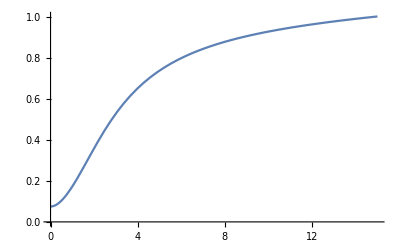

```mathematica
Plot[c2mrfun[0.001,-1.25,7.3,0.3,1.5,r],{r,0.005,15},AxesOrigin->{0,0}]
```

## Constraining Parameter space to a sphere

```mathematica
Quit[];
```

```mathematica
Clear[ϕ]
```

```mathematica
threesphere={}; (* Empty list to store values. *)
Numpoints=500; (* Number of random points to generate *)
centerμ1=-1.25;centerc=0.3; centerA=1.5; (* Parameter values for our particular solution which will be the central value in the sphere. *)
meanradius=1; (* Radius of the sphere. *)
sigmaradius=0.05(* Perturbed radius from the central values. *)
```

```mathematica
(* Generate random numbers for the radial distance, polar and azimuthal angles *)
θ=RandomVariate[NormalDistribution[0,N[Pi]],Numpoints];ϕ=RandomVariate[NormalDistribution[0,2N[Pi]],Numpoints];radius=RandomVariate[NormalDistribution[meanradius,sigmaradius],Numpoints];
```

```mathematica
(* Generating random numbers for the function parameters constrained to a sphere of radius 1. *)
μ1randosphere=centerμ1+(radius*Sin[θ]*Cos[ϕ]);
crandosphere=centerc+(radius*Sin[θ]*Sin[ϕ]);
Arandosphere=centerA+(radius*Cos[θ]);
ℛrandosphere=RandomVariate[PoissonDistribution[7.3],Numpoints]; (* Since we have 4 parameters, this extra dimension in our parameter space will indicate a color within the sphere with a colorbar as the legend. See the corresponding python file for this plot. *)
```

```mathematica
(* Saving parameter sets that will form the sphere to a list, 'threesphere', so that we can do a 3D plot. *)
For[i=1,i<Length[μ1randosphere]+1,i++,threesphere=Append[threesphere,{μ1randosphere[[i]],crandosphere[[i]],Arandosphere[[i]]}]]
```

```mathematica
fig1=ListPointPlot3D[threesphere]
```

-Graphics3D-

```mathematica
(* Generate list that includes all the parameters and export as a text file to replot in python. *)
foursphere={};
For[i=1,i<Length[μ1randosphere]+1,i++,foursphere=Append[foursphere,{μ1randosphere[[i]],ℛrandosphere[[i]],crandosphere[[i]],Arandosphere[[i]]}]]
```

```mathematica
Export["/Users/mariamcampbell/Documents/PHD/current projects/final anisotropic solutions/starobinsky4sphere500pts.txt",foursphere,"Table"]
```

/Users/mariamcampbell/Documents/PHD/current projects/final anisotropic solutions/starobinsky4sphere500pts.txt

```mathematica
(* Checking the causality condition, 0 <= Subscript[c, m,r]^2 <= 1, for α=0.001 at different values of r. Some combinations of random numbers will lead to infinite expressions or indeterminate -- ignore and let it run. *)
causalsphere={};
For[i=1,i<Length[c2mrfun[0.001,μ1randosphere,ℛrandosphere,crandosphere,Arandosphere,r]]+1,i++,If[0<c2mrfun[0.001,μ1randosphere[[i]],ℛrandosphere[[i]],crandosphere[[i]],Arandosphere[[i]],0.005]<=1&&(0<c2mrfun[0.001,μ1randosphere[[i]],ℛrandosphere[[i]],crandosphere[[i]],Arandosphere[[i]],1]<=1)&&(0<c2mrfun[0.001,μ1randosphere[[i]],ℛrandosphere[[i]],crandosphere[[i]],Arandosphere[[i]],6]<=1),causalsphere=Append[causalsphere,{μ1randosphere[[i]],ℛrandosphere[[i]],crandosphere[[i]],Arandosphere[[i]]}]]]
```

```mathematica
Length[causalsphere] (* The number of sets of parameters that satisfies the causal condition*)
```

106

```mathematica
(* Export the list of parameter sets that obeys causality to a text file. This will be plotted in python. *)
Export["/Users/mariamcampbell/Documents/PHD/current projects/final anisotropic solutions/starobinskycausalsphere500pts.txt",causalsphere,"Table"]
```

/Users/mariamcampbell/Documents/PHD/current projects/final anisotropic solutions/starobinskycausalsphere500pts.txt

```mathematica
(* Substituting all parameter sets that obey causality back into the function Subscript[c, m,r]^2, and plot to check that it indeed satisfies causality. *)
causalsphereplots={};
For[i=1,i<Length[causalsphere]+1,i++,causalsphereplots=Append[causalsphereplots,c2mrfun[0.001,causalsphere[[i]][[1]],causalsphere[[i]][[2]],causalsphere[[i]][[3]],causalsphere[[i]][[4]],r]]]
```

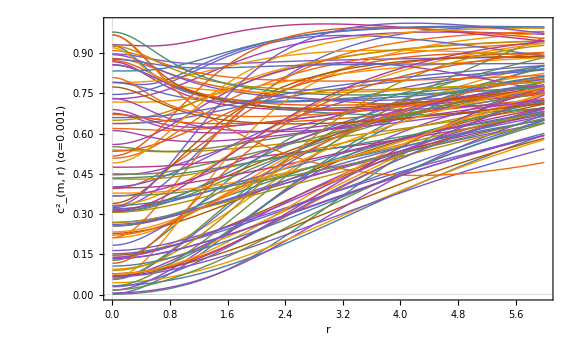

```mathematica
Plot[causalsphereplots,{r,0.005,6},AxesOrigin->{0,0},PlotStyle->{Thick},PlotTheme->"Scientific",LabelStyle->{FontSize->18,FontFamily->"Times"},Frame->{{True,True},{True,True}},FrameLabel->{r,"(c^2)_(m, r) (α=0.001)"},ImageSize->Large]
```

```mathematica
(* Checking what the 3 sphere looks like where causality is obeyed. *)
causal3sphere={};
For[i=1,i<Length[c2mrfun[0.001,μ1randosphere,ℛrandosphere,crandosphere,Arandosphere,r]]+1,i++,If[0<c2mrfun[0.001,μ1randosphere[[i]],ℛrandosphere[[i]],crandosphere[[i]],Arandosphere[[i]],0.005]<=1&&(0<c2mrfun[0.001,μ1randosphere[[i]],ℛrandosphere[[i]],crandosphere[[i]],Arandosphere[[i]],1]<=1)&&(0<c2mrfun[0.001,μ1randosphere[[i]],ℛrandosphere[[i]],crandosphere[[i]],Arandosphere[[i]],6]<=1),causal3sphere=Append[causal3sphere,{μ1randosphere[[i]],crandosphere[[i]],Arandosphere[[i]]}]]]
```

```mathematica
fig2=ListPointPlot3D[causal3sphere,PlotStyle->Red] (* 3D figure for parameters obeying causality. *)
```

-Graphics3D-

```mathematica
Show[fig1,fig2] (* Overlaying causality parameters to all random points generated. *)
```

-Graphics3D-